# tauAlphaTable

## data loading

```mathematica
p0s={3.9,3.85,3.825,3.80,3.775,3.75};
```

```mathematica
temperatures={{0.039,0.01,0.005,0.002,0.001,0.0005,0.00033,0.00014,0.000091,0.000077,0.000054,0.000045,0.000036},{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.03105, 0.025 ,0.02 ,0.016 ,0.012, 0.01, 0.009 ,0.008 ,0.0075, 0.007 ,0.0063, 0.0056 ,0.0054},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{999999, 999999, 999999,999999,46.2416,35.0693,135.321,564.239,829.48,897.484,1365.27,1522.57,3000},{ 999999, 999999, 999999,999999, 999999,60, 80, 200, 500, 800, 999999, 999999, 999999,999999, 999999, 999999, 999999},{ 999999, 999999, 999999,999999, 999999,25, 40 ,60, 80, 120,200 ,300 ,1000 ,999999, 999999,999999},{ 999999, 999999, 999999,999999, 999999,40 ,70 ,150 ,250, 600 ,2000, 999999 ,999999, 999999},{ 999999, 999999, 999999 ,30, 80 ,100 ,400 ,500 ,2500 ,2500, 3000 ,7000, 10000},{ 999999, 999999, 999999,10 ,30 ,70, 150 ,700,1400, 4000 ,9500}};
```

```mathematica
CRoverlap=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeCRoverlap_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeCRoverlap_N4096_p3.9000_T0.00100000_waitingTime10000_idx17.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeCRoverlap_N4096_p3.9000_T0.00100000_waitingTime10000_idx18.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeCRoverlap_N4096_p3.9000_T0.00050000_waitingTime10000_idx16.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
CRSISF=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeCRSISF_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]
],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeCRSISF_N4096_p3.9000_T0.00100000_waitingTime10000_idx17.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeCRSISF_N4096_p3.9000_T0.00100000_waitingTime10000_idx18.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeCRSISF_N4096_p3.9000_T0.00050000_waitingTime10000_idx16.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
time=Table[Table[Table[Mean[DeleteCases[Table[CRSISF[[p,T,i,1,rec]],{i,Length[CRSISF[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[CRSISF[[p,T,i,1]]],{i,Length[CRSISF[[p,T]]]}]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 640 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
CRoverlapMean=Table[Table[Table[Mean[DeleteCases[Table[CRoverlap[[p,T,i,2,rec]],{i,Length[CRoverlap[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[CRoverlap[[p,T,i,1]]],{i,Length[CRoverlap[[p,T]]]}]]-1}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 114 of … does not exist.

Part::partw: Part 115 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
CRSISFMean=Table[Table[Table[Mean[DeleteCases[Table[CRSISF[[p,T,i,2,rec]],{i,Length[CRSISF[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[CRSISF[[p,T,i,1]]],{i,Length[CRSISF[[p,T]]]}]]-1}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 114 of … does not exist.

Part::partw: Part 115 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
absTime=Table[Table[Table[time[[p,T,rec+1]]-time[[p,T,1]],{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

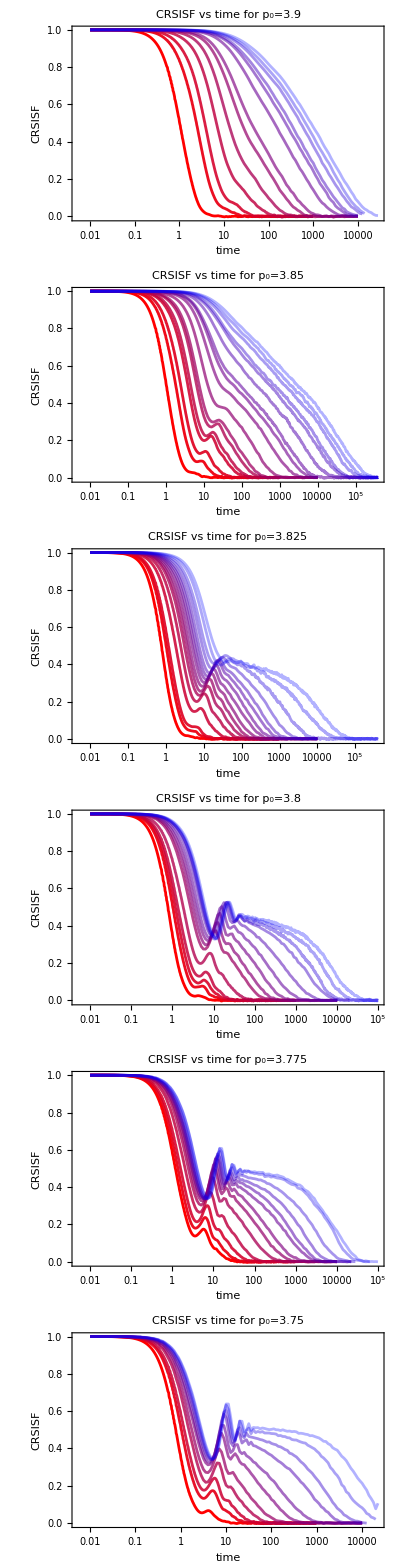

```mathematica
CRSISFMeanPlots=Table[Show[
ListLogLinearPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True]],{p,Length[p0s]}];
Column[CRSISFMeanPlots]
```

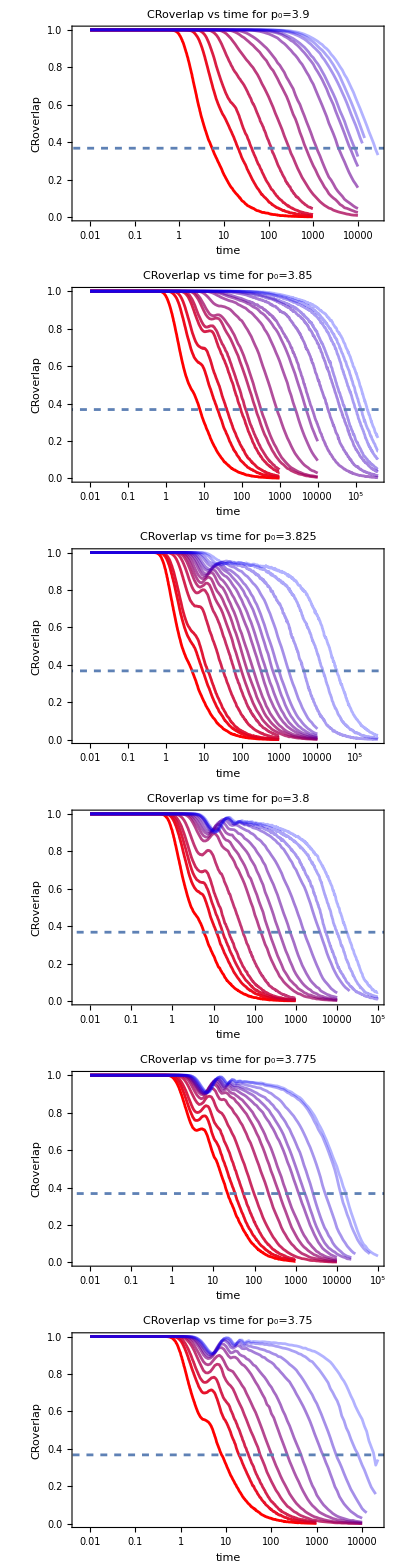

```mathematica
CRoverlapMeanPlots=Table[Show[
ListLogLinearPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRoverlapMean[[p,T,rec]]},{rec,Length[CRoverlapMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time for p_0="<>ToString[p0s[[p]]],Joined->True],LogLinearPlot[1/E,{x,0.001,1000000},PlotStyle->Dashed]],{p,Length[p0s]}];
Column[CRoverlapMeanPlots]
```

## Get τ_α

### fit CRSISF to stretched exponential

#### initial fitting

```mathematica
CRSISFMeanArtificalExtend=CRSISFMean;
artificialTime=absTime[[2]];
```

```mathematica
Table[artificialTime[[i]]=Flatten[Append[artificialTime[[i]],Table[N[10^(4+i/20)],{i,20}]]];,{i,9,10}];
Table[artificialTime[[i]]=Flatten[Append[artificialTime[[i]],Table[N[10^(4+i/100)],{i,100}]]];,{i,11,Length[artificialTime]}];
```

```mathematica
Table[CRSISFMeanArtificalExtend[[2,i]]=Flatten[Append[CRSISFMeanArtificalExtend[[2,i]],Table[0,{i,20}]]];,{i,9,10}];
Table[CRSISFMeanArtificalExtend[[2,i]]=Flatten[Append[CRSISFMeanArtificalExtend[[2,i]],Table[0,{i,30}]]];,{i,11,Length[CRSISFMeanArtificalExtend[[2]]]}];
```

```mathematica
Flatten[Append[{0,0,0},{1,1,2}]]
```

{0,0,0,1,1,2}

```mathematica
Table[a=i;,{i,10}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[CRSISFMeanArtificalExtend[[2,i]]=Flatten[Append[CRSISFMeanArtificalExtend[[2,i]],Table[0,{i,20}]]];,{i,10,Length[CRSISFMeanArtificalExtend[[2]]]}];
```

```mathematica
CRSISFMeanArtificalExtend[[2,10,100;;]]
```

{0.0474919,0.0354673,0.0280348,0.0212351,0.0134375,0.0094915,0.00436318,0.00149991,-0.0000979475,-0.0012106,-0.00134944,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[N[10^(4+i/20)],{i,20}]
```

{11220.2,12589.3,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

101

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
fitStartNum={{4.475071152747874,11.652430079375243,20.605149307413377,28.98332354454631,43.181917710603976,52.40218049256373,60.75745364744918,70.43274879137778,74.56208470027373,75.41395136154124,76.2623562138542,76.25356126410557,76.25136268515374},{4.746813237004902,9.4598018063875,11.733682063000668,15.866552523746426,18.857083790143243,23.396892354511074,26.06716697056073,28.407935830446753,33.75497584997275,44.69759769708517,100,100,100,100,100,100,100},{4.181227597599696,6.601632624506163,7.754920469258849,10.846794645005172,16.462632220584393,21.83945522645316,21.252851360922705,23.986133137043076,26.71034271282561,28.95468707418388,29.742850824887917,30.967225782497586,34.954383218327905,42.77645128150349,53.0586027290876,55.991675432346526},{5.5443851977847185,8.543302161661563,10.801556831371771,11.484500787075994,14.159855162331585,16.415770244286062,18.57272413948379,22.353104396049027,23.776138167085982,28.267010584971434,32.38112550556924,42.49938985840521,44.65269580110065,44.10416308353813},{12.275005769964972,13.3900602507303,14.607287299171793,18.46868551379298,21.686557895506116,24.53417261923667,25.778256389405044,32.17535373224476,39.18657032041287,41.68125213915501,45.43737491934978,45,45},{5.22625330341219,8.757313686570457,9.787122180079717,11.705078819553803,14.159218058513453,17.924491941701763,19.168324645208596,25.675629384707115,29.712549254051698,31.78020274296657,34.77161632608988}};
```

```mathematica
fitStartNum={{4.475071152747874,11.652430079375243,20.605149307413377,28.98332354454631,43.181917710603976,52.40218049256373,60.75745364744918,1000,1000,1000,1000,1000,1000},{4.746813237004902,9.4598018063875,11.733682063000668,15.866552523746426,18.857083790143243,23.396892354511074,26.06716697056073,28.407935830446753,100,500,1000,1000,5000,10000,10000,10000,10000},{4.181227597599696,6.601632624506163,5,7,16.462632220584393,21.83945522645316,21.252851360922705,23.986133137043076,26.71034271282561,28.95468707418388,29.742850824887917,30.967225782497586,34.954383218327905,300,500,500},{5.5443851977847185,8.543302161661563,10.801556831371771,11.484500787075994,14.159855162331585,16.415770244286062,18.57272413948379,22.353104396049027,23.776138167085982,100,500,500,500,500},{12.275005769964972,13.3900602507303,14.607287299171793,18.46868551379298,21.686557895506116,24.53417261923667,25.778256389405044,32.17535373224476,300,300,300,300,300},{5.22625330341219,8.757313686570457,9.787122180079717,11.705078819553803,14.159218058513453,17.924491941701763,19.168324645208596,25.675629384707115,300,300,300}};
```

```mathematica
fitStartNum={{1,10,20,28.98332354454631,43.181917710603976,52.40218049256373,60.75745364744918,1000,1000,1000,1000,1000,1000},{4.746813237004902,9.4598018063875,11.733682063000668,15.866552523746426,18.857083790143243,23.396892354511074,26.06716697056073,28.407935830446753,100,500,500,1000,5000,5000,10000,10000,10000},{4.181227597599696,6.601632624506163,5,7,16.462632220584393,21.83945522645316,21.252851360922705,23.986133137043076,26.71034271282561,28.95468707418388,29.742850824887917,30.967225782497586,34.954383218327905,100,500,500},{5.5443851977847185,8.543302161661563,10.801556831371771,11.484500787075994,14.159855162331585,16.415770244286062,18.57272413948379,22.353104396049027,23.776138167085982,100,500,100,100,100},{12.275005769964972,13.3900602507303,14.607287299171793,18.46868551379298,21.686557895506116,24.53417261923667,25.778256389405044,32.17535373224476,39.18657032041287,41.68125213915501,45.43737491934978,45,45},{5.22625330341219,8.757313686570457,9.787122180079717,11.705078819553803,14.159218058513453,17.924491941701763,19.168324645208596,25.675629384707115,29.712549254051698,31.78020274296657,34.77161632608988}};
```

```mathematica
fitStartPos=Table[Table[Position[absTime[[p,i]],_?(#>fitStartNum[[p,i]]&)][[1,1]],{i,Length[fitStartNum[[p]]]}],{p,Length[p0s]}]
```

{{81,181,211,227,63,65,66,90,90,90,90,90,91},{148,178,187,201,208,58,59,60,70,84,350,380,450,450,481,480,480},{143,162,150,165,202,57,57,58,59,60,60,60,61,281,350,350},{155,174,184,187,196,55,56,57,58,70,84,280,280,281},{189,193,197,56,57,58,59,61,62,63,64,64,64},{152,175,180,52,54,56,56,59,60,61,61}}

```mathematica
fitEndPos=Table[Table[If[AllTrue[CRSISFMean[[p,i]],#>0&],Length[CRSISFMean[[p,i]]],Position[CRSISFMean[[p,i]],_?(#<10^-2.5&)][[1,1]]-1],{i,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{155,218,245,295,81,87,93,104,110,110,112,113,119},{188,228,252,294,298,80,82,90,102,106,474,527,558,560,596,605,624},{166,195,205,247,276,73,77,79,83,87,90,94,99,471,534,557},{174,200,215,225,267,79,81,86,95,101,110,486,513,542},{230,242,273,73,83,89,94,101,102,107,119,122,122},{188,227,250,68,76,84,92,110,109,116,117}}

```mathematica
fits=Table[Table[NonlinearModelFit[Table[{Normal[absTime[[p,T]][[rec]]],Normal[CRSISFMean[[p,T,rec]]]},{rec,fitStartPos[[p,T]],fitEndPos[[p,T]]}],{stretchedExp[t,G,τ,β],{0.999>β>0.6,0.8>G>0.4,50000>τ>0.5}},{{G,0.5},{τ,100},{β,0.8}},t],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
fitsGlobal=Table[Table[NonlinearModelFit[Table[{Normal[absTime[[p,T]][[rec]]],Normal[CRSISFMean[[p,T,rec]]]},{rec,fitStartPos[[p,T]],Length[CRSISFMean[[p,T]]]}],{stretchedExp[t,G,τ,0.8],{0.8>G>0.3,50000>τ>0.5}},{G,τ},t,MaxIterations->Automatic,Method->{"NMinimize",Method->{"RandomSearch","SearchPoints"->500}}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
fitsGlobal
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
Table[Table[absTime[[p,T]][[fitStartPos[[p,T]]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{1.02,10.23,20.42,29.51,44.67,56.23,63.1,501.19,501.19,501.19,501.19,501.19,501.19},{4.79,9.55,11.75,16.22,19.05,25.12,28.18,31.62,100.,501.19,1023.29,1000.,5011.87,10232.9,10232.9,10000.,10000.},{4.27,6.61,5.01,7.08,16.6,22.39,22.39,25.12,28.18,31.62,31.62,31.62,35.48,102.33,501.19,501.19},{5.62,8.71,10.96,11.75,14.45,17.78,19.95,22.39,25.12,100.,501.19,100.,100.,102.33},{12.3,13.49,14.79,19.95,22.39,25.12,28.18,35.48,39.81,44.67,50.12,50.12,50.12},{5.25,8.91,10.,12.59,15.85,19.95,19.95,28.18,31.62,35.48,35.48}}

```mathematica
fits[[1,1]][1]
```

0.336635

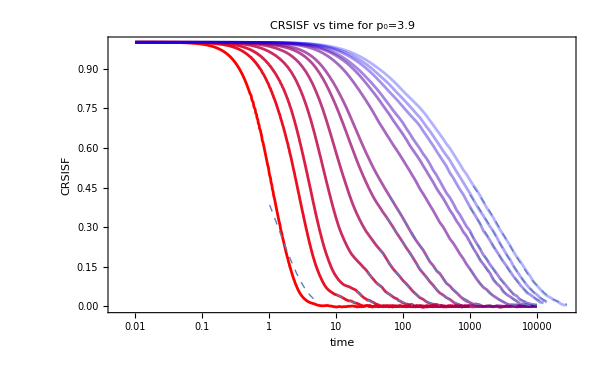
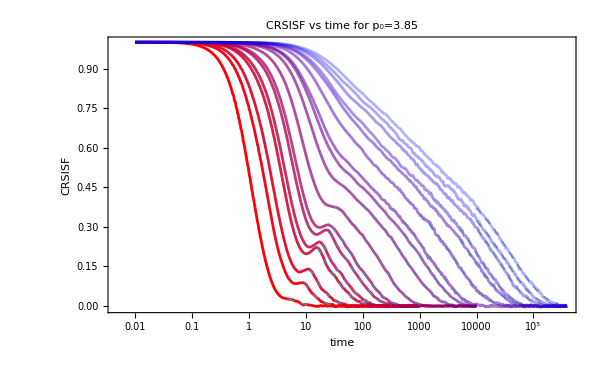
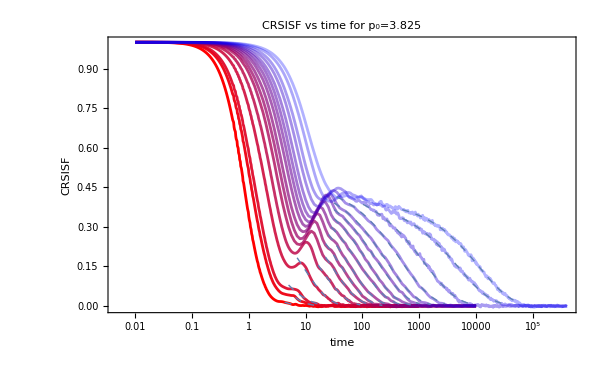
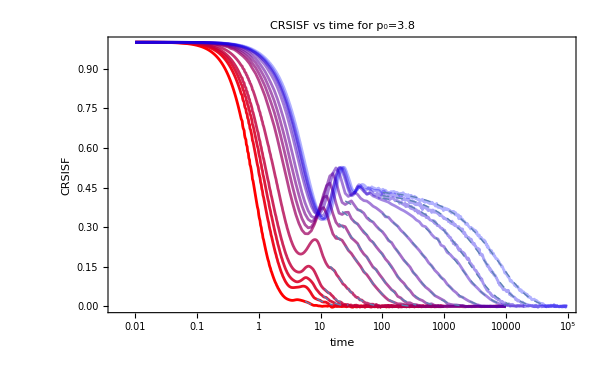
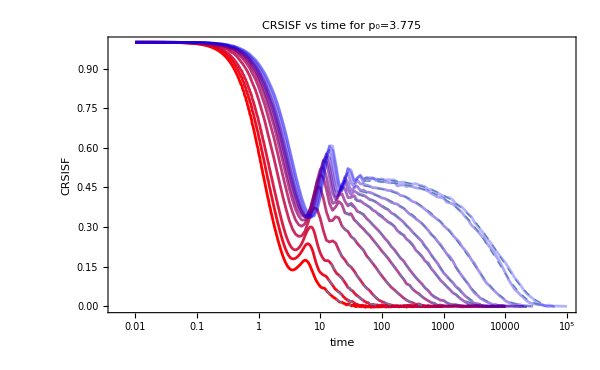
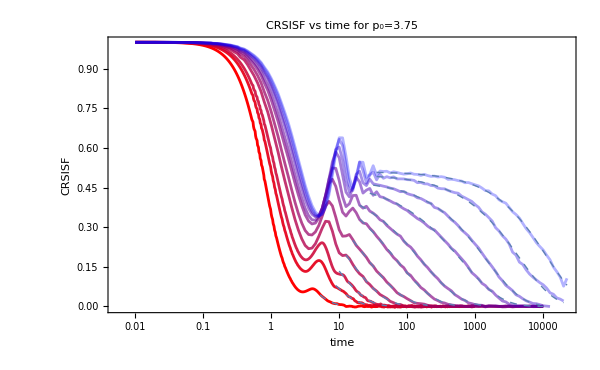

```mathematica
CRSISFFittingPlots=Table[Show[
ListLogLinearPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],Table[LogLinearPlot[fits[[p,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}]
```

```mathematica
betaSISFfitsTable=Table[Table[fits[[p,T]]["BestFitParameters"][[3,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.999,0.716409,0.963156,0.870235,0.871025,0.778736,0.657252,0.724749,0.867629,0.796791,0.716155,0.76989,0.69821},{0.654349,0.900747,0.738854,0.711213,0.777514,0.778683,0.844291,0.878643,0.767749,0.885281,0.804076,0.77776,0.836284,0.82868,0.860094,0.811893,0.73694},{0.604329,0.789135,0.725618,0.964847,0.908886,0.948448,0.981702,0.924922,0.857007,0.889453,0.807712,0.816899,0.773809,0.732038,0.742868,0.767357},{0.972253,0.803636,0.956974,0.997494,0.922618,0.97407,0.883182,0.87023,0.774625,0.738138,0.875634,0.925077,0.915335,0.864645},{0.840873,0.954266,0.938724,0.959829,0.82698,0.77532,0.750144,0.739536,0.808644,0.873329,0.82829,0.927227,0.863107},{0.791894,0.866751,0.949414,0.794262,0.736688,0.771335,0.749988,0.745488,0.837848,0.849516,0.908136}}

```mathematica
GSISFfitsTable=Table[Table[fits[[p,T]]["BestFitParameters"][[1,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.8,0.404212,0.425615,0.40074,0.474115,0.607526,0.75073,0.712469,0.554533,0.608563,0.70031,0.674466,0.73881},{0.40355,0.576659,0.796103,0.667651,0.530354,0.525774,0.470365,0.461283,0.500822,0.428743,0.400041,0.492078,0.448428,0.400173,0.469992,0.477748,0.534682},{0.409492,0.576569,0.400149,0.400031,0.40006,0.400267,0.400118,0.431873,0.438195,0.441896,0.467064,0.466472,0.473008,0.454911,0.400019,0.400004},{0.698414,0.408837,0.407873,0.410025,0.414125,0.400103,0.444543,0.450171,0.479433,0.470226,0.410983,0.430677,0.430996,0.441417},{0.581645,0.42009,0.400325,0.400371,0.452695,0.473472,0.486625,0.467583,0.466212,0.457409,0.472896,0.479735,0.490837},{0.791619,0.400412,0.400123,0.516654,0.530442,0.487426,0.471949,0.472481,0.477856,0.49981,0.510124}}

```mathematica
tauSISFfitsTable=Table[Table[fits[[p,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{1.38879,3.42038,9.93791,25.5118,58.8593,111.427,138.523,630.703,1084.94,1109.73,1581.35,2072.59,2807.26},{1.13644,4.75369,5.65715,14.1278,24.748,46.0005,74.7527,198.608,532.863,1276.8,1987.69,3978.31,9872.25,14510.1,23988.6,31680.5,39741.6},{0.575771,1.74147,2.5918,9.12762,17.6261,29.4542,43.1746,57.5928,87.2764,128.118,180.813,262.959,474.057,1193.96,4877.6,11440.1},{1.51697,2.58736,4.58341,6.43769,14.3992,45.602,65.8918,123.5,224.073,536.134,1791.8,2628.82,4960.98,7943.74},{4.72709,9.33229,16.2124,31.2999,68.6298,130.72,206.535,493.285,740.565,1363.65,2787.39,7222.87,8660.67},{1.37288,5.09918,9.08007,12.9821,23.332,67.9807,161.303,632.615,1472.,4476.39,11364.6}}

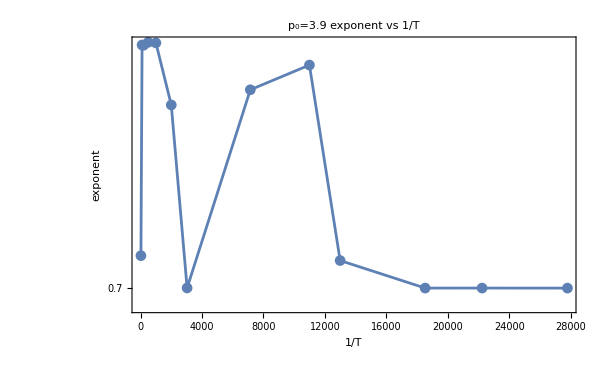
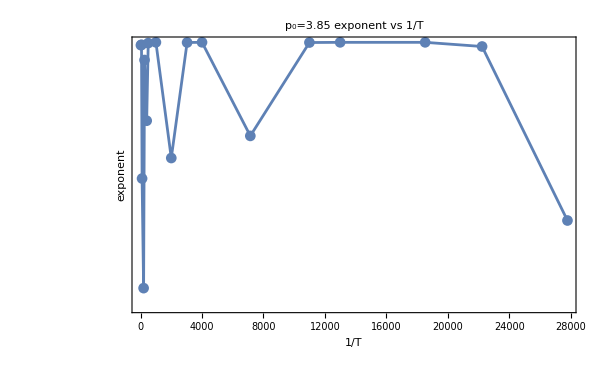
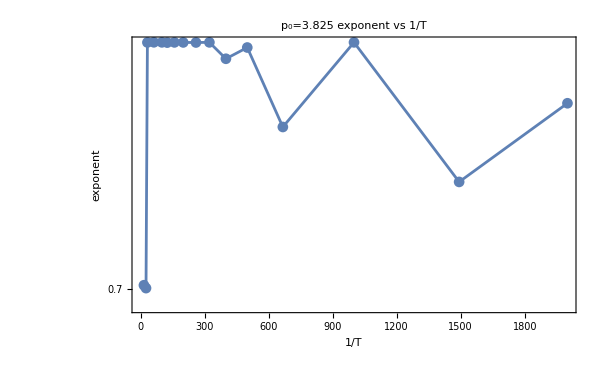
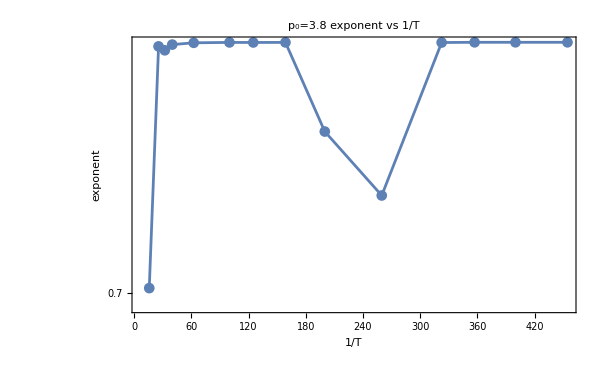
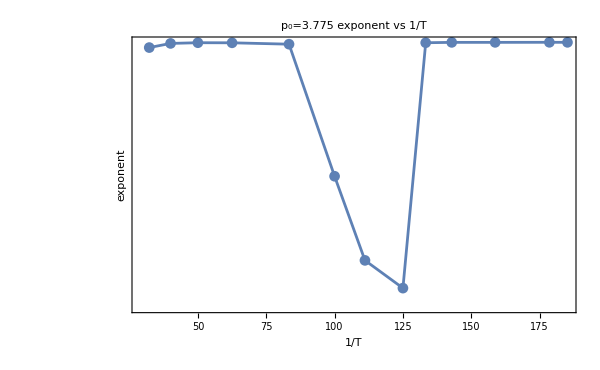
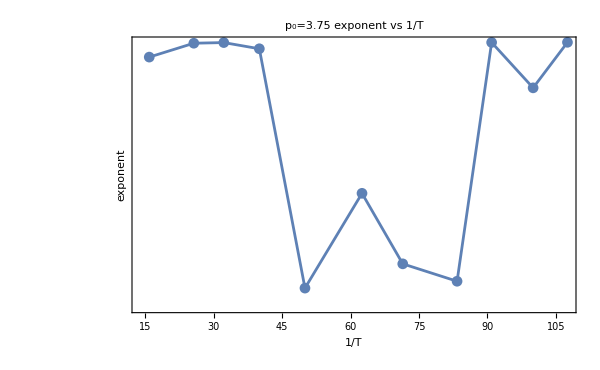

```mathematica
Table[ListLogPlot[Table[{1/temperatures[[p,T]],betaSISFfitsTable[[p,T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" exponent vs 1/T",Joined->True,PlotRange->All],{p,Length[p0s]}]
```

#### fit 3.825

```mathematica
insp=3;
```

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
fitStartNum={{1,10,20,28.98332354454631,43.181917710603976,52.40218049256373,60.75745364744918,1000,1000,1000,1000,1000,1000},{4.746813237004902,9.4598018063875,11.733682063000668,15.866552523746426,18.857083790143243,23.396892354511074,26.06716697056073,28.407935830446753,100,500,500,1000,5000,5000,10000,10000,10000},{4.181227597599696,6.601632624506163,5,7,16.462632220584393,30,35,40,45,60,100,100,100,200,300,300},{5.5443851977847185,8.543302161661563,10.801556831371771,11.484500787075994,14.159855162331585,16.415770244286062,18.57272413948379,22.353104396049027,23.776138167085982,100,500,100,100,100},{12.275005769964972,13.3900602507303,14.607287299171793,18.46868551379298,21.686557895506116,24.53417261923667,25.778256389405044,32.17535373224476,39.18657032041287,41.68125213915501,45.43737491934978,45,45},{5.22625330341219,8.757313686570457,9.787122180079717,11.705078819553803,14.159218058513453,17.924491941701763,19.168324645208596,25.675629384707115,29.712549254051698,31.78020274296657,34.77161632608988}};
```

```mathematica
fitStartPos=Table[Table[Position[absTime[[p,i]],_?(#>fitStartNum[[p,i]]&)][[1,1]],{i,Length[fitStartNum[[p]]]}],{p,Length[p0s]}]
```

{{81,181,211,227,63,65,66,90,90,90,90,90,91},{148,178,187,201,208,58,59,60,70,84,350,380,450,450,481,480,480},{143,162,150,165,202,60,61,63,64,66,70,70,70,311,328,328},{155,174,184,187,196,55,56,57,58,70,84,280,280,281},{189,193,197,56,57,58,59,61,62,63,64,64,64},{152,175,180,52,54,56,56,59,60,61,61}}

```mathematica
fitEndPos=Table[Table[If[AllTrue[CRSISFMean[[p,i]],#>0&],Length[CRSISFMean[[p,i]]],Position[CRSISFMean[[p,i]],_?(#<0.01&)][[1,1]]-1],{i,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{146,212,238,283,78,85,90,100,110,110,112,113,119},{170,214,243,277,293,77,81,88,99,104,468,515,546,554,583,597,617},{151,182,198,232,261,71,73,77,81,85,88,92,98,459,521,554},{163,192,203,215,257,74,79,84,91,99,107,479,509,534},{219,236,259,71,80,87,91,97,101,105,119,119,120},{177,215,232,66,74,81,89,110,108,116,117}}

```mathematica
betaConstrains={0.999>β>0.9,0.999>β>0.9,0.999>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.7,0.95>β>0.7,0.95>β>0.8,0.95>β>0.6,0.95>β>0.6,0.95>β>0.6}
```

{0.999>β>0.9,0.999>β>0.9,0.999>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.7,0.95>β>0.7,0.95>β>0.8,0.95>β>0.6,0.95>β>0.6,0.95>β>0.6}

```mathematica
gConstrains={0.99>G>0.5,0.99>G>0.5,0.44>G>0.38,0.44>G>0.38,0.44>G>0.38,0.44>G>0.38,0.44>G>0.38,0.44>G>0.38,0.44>G>0.38,0.42>G>0.38,0.42>G>0.38,0.42>G>0.38,0.42>G>0.38,0.5>G>0.3,0.5>G>0.3,0.5>G>0.3};
```

```mathematica
10^0.8
```

6.30957

```mathematica
fits=Table[Table[NonlinearModelFit[Table[{Normal[absTime[[p,T]][[rec]]],Normal[CRSISFMean[[p,T,rec]]]},{rec,fitStartPos[[p,T]],fitEndPos[[p,T]]}],{stretchedExp[t,G,τ,β],{betaConstrains[[T]],gConstrains[[T]],50000>τ&&τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[p]]]}],{p,3,3}];
```

```mathematica
10^(Log10[tauCRSISFfits[[1]]]+0.2)
```

1.44892

```mathematica
tauConstraints=Table[10^(Log10[tauCRSISFfits[[i]]]+0.2)>τ&&τ>10^(Log10[tauCRSISFfits[[i]]]-0.2),{i,Length[temperatures[[insp]]]}]
```

{1.44889>τ&&τ>0.576815,2.96836>τ&&τ>1.18173,4.77334>τ&&τ>1.9003,12.7302>τ&&τ>5.06797,25.1767>τ&&τ>10.023,41.2153>τ&&τ>16.4081,59.7607>τ&&τ>23.7912,86.8922>τ&&τ>34.5924,137.651>τ&&τ>54.7998,213.84>τ&&τ>85.1311,324.806>τ&&τ>129.308,480.494>τ&&τ>191.288,893.225>τ&&τ>355.599,2048.82>τ&&τ>815.652,7486.89>τ&&τ>2980.59,18214.5>τ&&τ>7251.34}

```mathematica
fitsFixedG=Table[Table[NonlinearModelFit[Table[{Normal[absTime[[p,T]][[rec]]],Normal[CRSISFMean[[p,T,rec]]]},{rec,fitStartPos[[p,T]],fitEndPos[[p,T]]}],{stretchedExp[t,0.4,τ,β],{betaConstrains[[T]],tauConstraints[[T]]}},{τ,β},t],{T,Length[temperatures[[p]]]}],{p,insp,insp}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
fits
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
Length[temperatures[[insp]]]
```

16

```mathematica
plateauSISFfits=Table[fits[[1,T]]["BestFitParameters"][[1,2]],{T,Length[temperatures[[insp]]]}]
```

{0.506664,0.501149,0.380017,0.401849,0.380089,0.437972,0.41581,0.438149,0.409814,0.419911,0.388684,0.419469,0.419959,0.435138,0.40878,0.39898}

```mathematica
betaSISFfitsTable=Table[fits[[1,T]]["BestFitParameters"][[3,2]],{T,Length[temperatures[[insp]]]}]
```

{0.903301,0.900596,0.900022,0.949948,0.926181,0.929122,0.94939,0.907782,0.900569,0.933488,0.948993,0.920172,0.902693,0.769316,0.722004,0.77249}

```mathematica
tauCRSISFfits=Table[fits[[1,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[insp]]]}]
```

{1.07264,2.20405,3.24774,9.04827,18.5243,27.4679,41.3771,56.3273,94.5719,136.194,227.481,303.422,563.195,1282.48,4711.04,11490.9}

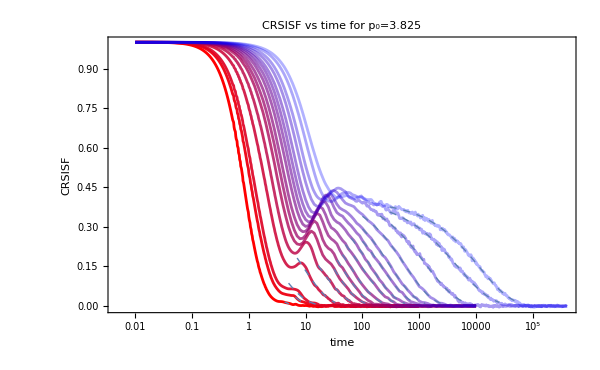
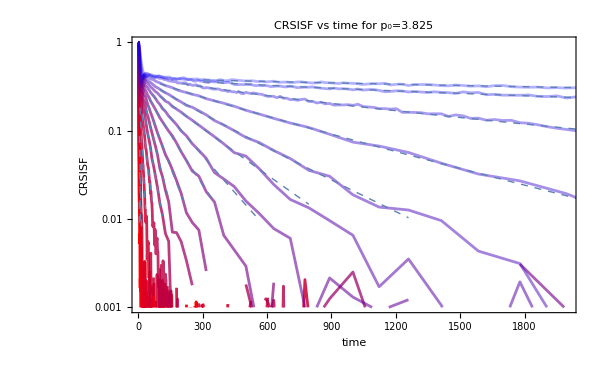
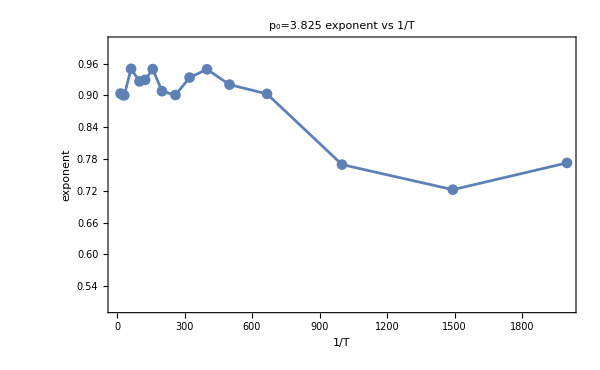
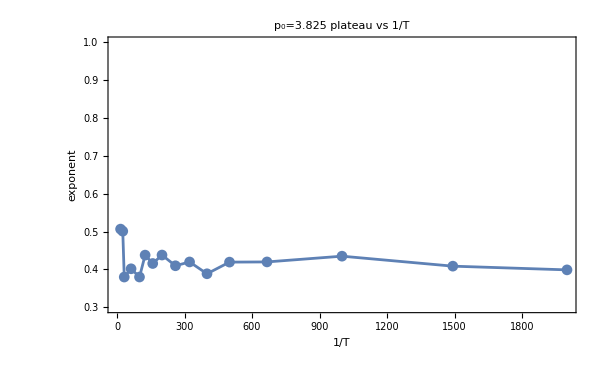
Grid[{-Graphics-,-Graphics-,-Graphics-,-Graphics-},2]

```mathematica
Grid[{Table[Show[
ListLogLinearPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],Table[LogLinearPlot[fits[[1,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick}],{T,Length[temperatures[[p]]]}]],{p,3,3}][[1]],Table[Show[
ListLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{10,2000},{0.001,1}}],Table[LogPlot[fits[[1,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick}],{T,Length[temperatures[[p]]]}]],{p,3,3}][[1]],Table[ListPlot[Table[{1/temperatures[[p,T]],betaSISFfitsTable[[T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" exponent vs 1/T",Joined->True,PlotRange->{All,{0.5,1}}],{p,insp,insp}][[1]],Table[ListPlot[Table[{1/temperatures[[p,T]],plateauSISFfits[[T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" plateau vs 1/T",Joined->True,PlotRange->{All,{0.3,1}}],{p,insp,insp}][[1]]},2]
```

#### fit 3.90

```mathematica
insp=1;
```

```mathematica
Length[temperatures[[insp]]]
```

13

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
fitStartNum={{2,10,20,28.98332354454631,43.181917710603976,52.40218049256373,60.75745364744918,300,600,600,1000,1000,1000},{4.746813237004902,9.4598018063875,11.733682063000668,15.866552523746426,18.857083790143243,23.396892354511074,26.06716697056073,28.407935830446753,100,500,500,1000,5000,5000,10000,10000,10000},{4.181227597599696,6.601632624506163,5,7,16.462632220584393,21.83945522645316,21.252851360922705,23.986133137043076,26.71034271282561,28.95468707418388,29.742850824887917,30.967225782497586,34.954383218327905,100,300,300},{5.5443851977847185,8.543302161661563,10.801556831371771,11.484500787075994,14.159855162331585,16.415770244286062,18.57272413948379,22.353104396049027,23.776138167085982,100,500,100,100,100},{12.275005769964972,13.3900602507303,14.607287299171793,18.46868551379298,21.686557895506116,24.53417261923667,25.778256389405044,32.17535373224476,39.18657032041287,41.68125213915501,45.43737491934978,45,45},{5.22625330341219,8.757313686570457,9.787122180079717,11.705078819553803,14.159218058513453,17.924491941701763,19.168324645208596,25.675629384707115,29.712549254051698,31.78020274296657,34.77161632608988}};
```

```mathematica
fitStartPos=Table[Table[Position[absTime[[p,i]],_?(#>fitStartNum[[p,i]]&)][[1,1]],{i,Length[fitStartNum[[p]]]}],{p,Length[p0s]}]
```

{{111,181,211,227,63,65,66,80,86,86,90,90,91},{148,178,187,201,208,58,59,60,70,84,350,380,450,450,481,480,480},{143,162,150,165,202,57,57,58,59,60,60,60,61,281,328,328},{155,174,184,187,196,55,56,57,58,70,84,280,280,281},{189,193,197,56,57,58,59,61,62,63,64,64,64},{152,175,180,52,54,56,56,59,60,61,61}}

```mathematica
fitEndPos=Table[Table[If[AllTrue[CRSISFMean[[p,i]],#>0&],Length[CRSISFMean[[p,i]]],Position[CRSISFMean[[p,i]],_?(#<10^-2.5&)][[1,1]]-1],{i,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{155,218,245,295,81,87,93,104,110,110,112,113,119},{188,228,252,294,298,80,82,90,102,106,474,527,558,560,596,605,624},{166,195,205,247,276,73,77,79,83,87,90,94,99,471,534,557},{174,200,215,225,267,79,81,86,95,101,110,486,513,542},{230,242,273,73,83,89,94,101,102,107,119,122,122},{188,227,250,68,76,84,92,110,109,116,117}}

```mathematica
betaConstrains={0.99>β>0.5,0.999>β>0.7,0.8>β>0.7,0.999>β>0.7,0.999>β>0.6,0.999>β>0.6,0.72>β>0.6,0.75>β>0.55,0.77>β>0.75,0.75>β>0.55,0.75>β>0.55,0.78>β>0.75,0.75>β>0.55}
```

{0.99>β>0.5,0.999>β>0.7,0.8>β>0.7,0.999>β>0.7,0.999>β>0.6,0.999>β>0.6,0.72>β>0.6,0.75>β>0.55,0.77>β>0.75,0.75>β>0.55,0.75>β>0.55,0.78>β>0.75,0.75>β>0.55}

```mathematica
gConstrains={0.99>G>0.7,0.7>G>0.6,0.7>G>0.6,0.7>G>0.6,0.7>G>0.6,0.7>G>0.6,0.7>G>0.6,0.99>G>0.4,0.99>G>0.4,0.99>G>0.4,0.99>G>0.4,0.99>G>0.4,0.99>G>0.4};
```

```mathematica
fits=Table[Table[NonlinearModelFit[Table[{Normal[absTime[[p,T]][[rec]]],Normal[CRSISFMean[[p,T,rec]]]},{rec,fitStartPos[[p,T]],fitEndPos[[p,T]]}],{stretchedExp[t,G,τ,β],{betaConstrains[[T]],gConstrains[[T]],50000>τ>0.5}},{{G},{τ},{β}},t],{T,Length[temperatures[[p]]]}],{p,insp,insp}];
```

```mathematica
fits
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
Length[temperatures[[insp]]]
```

16

```mathematica
plateauSISFfits=Table[fits[[1,T]]["BestFitParameters"][[1,2]],{T,Length[temperatures[[insp]]]}]
```

{0.989967,0.600337,0.69769,0.600385,0.600351,0.608211,0.69992,0.645404,0.653645,0.669239,0.700541,0.674641,0.738899}

```mathematica
betaSISFfitsTable=Table[fits[[1,T]]["BestFitParameters"][[3,2]],{T,Length[temperatures[[insp]]]}]
```

{0.989987,0.700131,0.799261,0.712127,0.746842,0.777999,0.697557,0.749204,0.769852,0.748215,0.715955,0.769685,0.698128}

```mathematica
{0.9225667337378314,0.6002981301973063,0.7741797546838524,0.6659184479828183,0.6833542857528847,0.6321256056354989,0.6571634958147435,0.7198166404594938,0.7199209846252685,0.7198211712453488,0.715022209850623,0.7199262016115247,0.6980841985138433}
```

{0.922567,0.600298,0.77418,0.665918,0.683354,0.632126,0.657163,0.719817,0.719921,0.719821,0.715022,0.719926,0.698084}

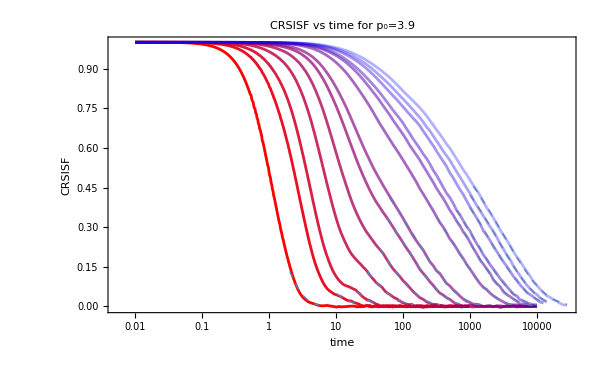
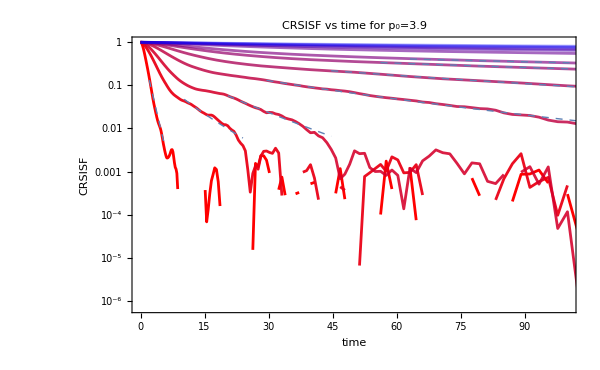
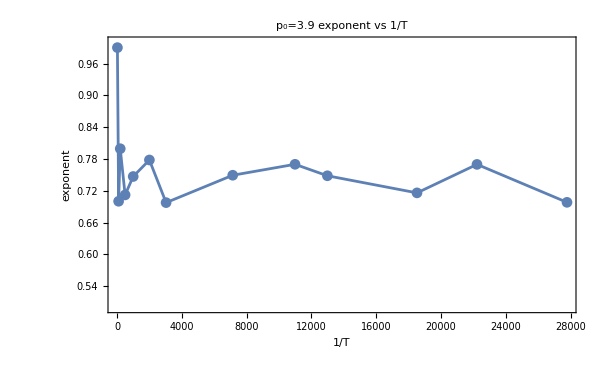
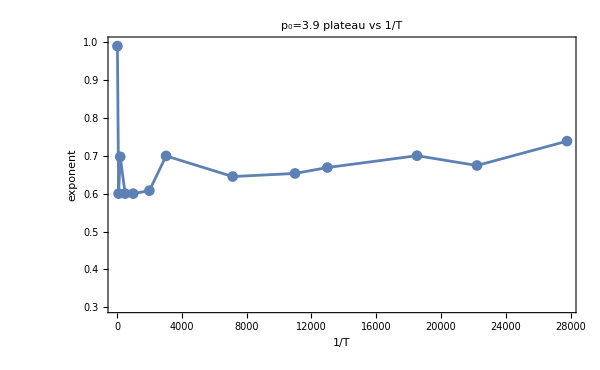
Grid[{-Graphics-,-Graphics-,-Graphics-,-Graphics-},2]

```mathematica
Grid[{Table[Show[
ListLogLinearPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],Table[LogLinearPlot[fits[[1,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick}],{T,Length[temperatures[[p]]]}]],{p,insp,insp}][[1]],Table[Show[
ListLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{0,100},All}],Table[LogPlot[fits[[1,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick}],{T,Length[temperatures[[p]]]}]],{p,insp,insp}][[1]],Table[ListPlot[Table[{1/temperatures[[p,T]],betaSISFfitsTable[[T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" exponent vs 1/T",Joined->True,PlotRange->{All,{0.5,1.0}}],{p,insp,insp}][[1]],Table[ListPlot[Table[{1/temperatures[[p,T]],plateauSISFfits[[T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" plateau vs 1/T",Joined->True,PlotRange->{All,{0.3,1.0}}],{p,insp,insp}][[1]]},2]
```

```mathematica
fit 3.90
```

```mathematica
fit 3.90
```

#### fit 3.85

```mathematica
insp=2;
```

```mathematica
1/temperatures[[insp]]
```

{25.641,62.5,100.,200.,259.74,400.,500.,1000.,2000.,3030.3,4000.,7142.86,10989.,12987.,18518.5,22222.2,27777.8}

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
fitStartNum={{2,10,20,28.98332354454631,43.181917710603976,52.40218049256373,60.75745364744918,300,600,600,1000,1000,1000},{4.746813237004902,9.4598018063875,11.733682063000668,15.866552523746426,18.857083790143243,23.396892354511074,26.06716697056073,28.407935830446753,100,500,500,1000,5000,5000,10000,10000,10000},{4.181227597599696,6.601632624506163,5,7,16.462632220584393,21.83945522645316,21.252851360922705,23.986133137043076,26.71034271282561,28.95468707418388,29.742850824887917,30.967225782497586,34.954383218327905,100,300,300},{5.5443851977847185,8.543302161661563,10.801556831371771,11.484500787075994,14.159855162331585,16.415770244286062,18.57272413948379,22.353104396049027,23.776138167085982,100,500,100,100,100},{12.275005769964972,13.3900602507303,14.607287299171793,18.46868551379298,21.686557895506116,24.53417261923667,25.778256389405044,32.17535373224476,39.18657032041287,41.68125213915501,45.43737491934978,45,45},{5.22625330341219,8.757313686570457,9.787122180079717,11.705078819553803,14.159218058513453,17.924491941701763,19.168324645208596,25.675629384707115,29.712549254051698,31.78020274296657,34.77161632608988}};
```

```mathematica
fitStartPos=Table[Table[Position[absTime[[p,i]],_?(#>fitStartNum[[p,i]]&)][[1,1]],{i,Length[fitStartNum[[p]]]}],{p,Length[p0s]}]
```

{{111,181,211,227,63,65,66,80,86,86,90,90,91},{148,178,187,201,208,58,59,60,70,84,350,380,450,450,481,480,480},{143,162,150,165,202,57,57,58,59,60,60,60,61,281,328,328},{155,174,184,187,196,55,56,57,58,70,84,280,280,281},{189,193,197,56,57,58,59,61,62,63,64,64,64},{152,175,180,52,54,56,56,59,60,61,61}}

```mathematica
fitEndPos=Table[Table[If[AllTrue[CRSISFMean[[p,i]],#>0&],Length[CRSISFMean[[p,i]]],Position[CRSISFMean[[p,i]],_?(#<10^-2.5&)][[1,1]]-1],{i,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{155,218,245,295,81,87,93,104,110,110,112,113,119},{188,228,252,294,298,80,82,90,102,106,474,527,558,560,596,605,624},{166,195,205,247,276,73,77,79,83,87,90,94,99,471,534,557},{174,200,215,225,267,79,81,86,95,101,110,486,513,542},{230,242,273,73,83,89,94,101,102,107,119,122,122},{188,227,250,68,76,84,92,110,109,116,117}}

```mathematica
betaConstrains={0.99>β>0.9,0.99>β>0.8,0.85>β>0.75,0.85>β>0.75,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.8}
```

{0.99>β>0.9,0.99>β>0.8,0.85>β>0.75,0.85>β>0.75,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.8}

```mathematica
gConstrains={0.55>G>0.45,0.55>G>0.45,0.55>G>0.45,0.55>G>0.45,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3};
```

```mathematica
fits=Table[Table[NonlinearModelFit[Table[{Normal[absTime[[p,T]][[rec]]],Normal[CRSISFMean[[p,T,rec]]]},{rec,fitStartPos[[p,T]],fitEndPos[[p,T]]}],{stretchedExp[t,G,τ,β],{betaConstrains[[T]],gConstrains[[T]],50000>τ>0.5}},{{G},{τ},{β}},t],{T,Length[temperatures[[p]]]}],{p,insp,insp}];
```

```mathematica
fits
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
Length[temperatures[[insp]]]
```

16

```mathematica
plateauSISFfits=Table[fits[[1,T]]["BestFitParameters"][[1,2]],{T,Length[temperatures[[insp]]]}]
```

{0.450216,0.53701,0.549939,0.549904,0.530354,0.52578,0.470359,0.461281,0.500823,0.428688,0.473697,0.492078,0.448416,0.483952,0.469989,0.477747,0.499835}

```mathematica
betaSISFfitsTable=Table[fits[[1,T]]["BestFitParameters"][[3,2]],{T,Length[temperatures[[insp]]]}]
```

{0.900125,0.926085,0.849946,0.796561,0.777513,0.778674,0.8443,0.878647,0.767747,0.885394,0.804078,0.77776,0.836303,0.828683,0.860098,0.811895,0.800011}

```mathematica
{0.9225667337378314,0.6002981301973063,0.7741797546838524,0.6659184479828183,0.6833542857528847,0.6321256056354989,0.6571634958147435,0.7198166404594938,0.7199209846252685,0.7198211712453488,0.715022209850623,0.7199262016115247,0.6980841985138433}
```

{0.922567,0.600298,0.77418,0.665918,0.683354,0.632126,0.657163,0.719817,0.719921,0.719821,0.715022,0.719926,0.698084}

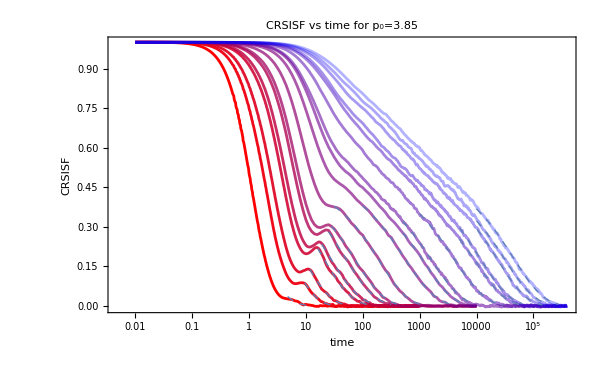
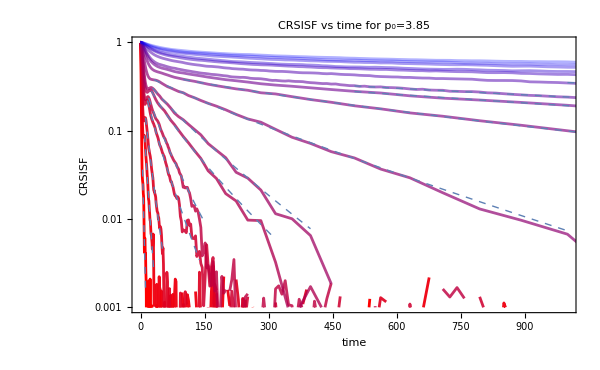
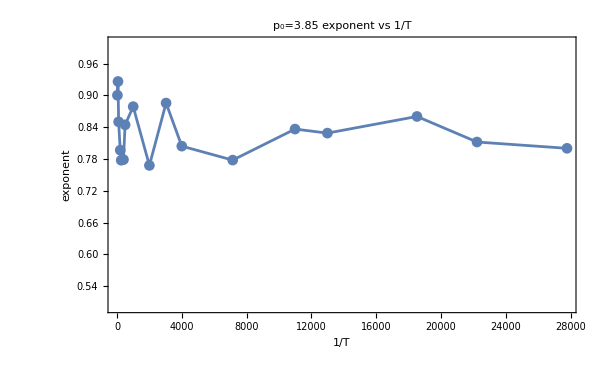
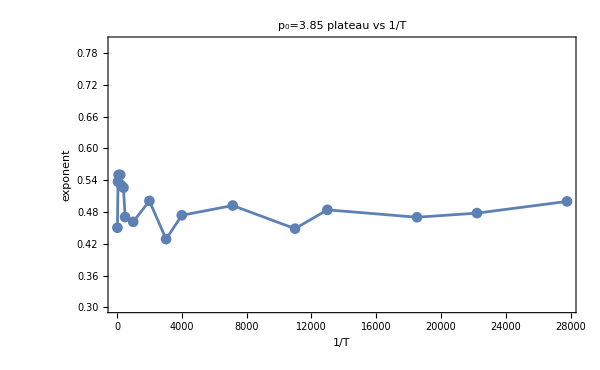
Grid[{-Graphics-,-Graphics-,-Graphics-,-Graphics-},2]

```mathematica
Grid[{Table[Show[
ListLogLinearPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],Table[LogLinearPlot[fits[[1,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick}],{T,Length[temperatures[[p]]]}]],{p,insp,insp}][[1]],Table[Show[
ListLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{0,1000},{0.001,1}}],Table[LogPlot[fits[[1,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick}],{T,Length[temperatures[[p]]]}]],{p,insp,insp}][[1]],Table[ListPlot[Table[{1/temperatures[[p,T]],betaSISFfitsTable[[T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" exponent vs 1/T",Joined->True,PlotRange->{All,{0.5,1.0}}],{p,insp,insp}][[1]],Table[ListPlot[Table[{1/temperatures[[p,T]],plateauSISFfits[[T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" plateau vs 1/T",Joined->True,PlotRange->{All,{0.3,0.8}}],{p,insp,insp}][[1]]},2]
```

```mathematica
fit 3.90
```

```mathematica
fit 3.90
```

#### fit 3.75

```mathematica
insp=6;
```

```mathematica
Length[temperatures[[insp]]]
```

11

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
fitStartNum={{2,10,20,28.98332354454631,43.181917710603976,52.40218049256373,60.75745364744918,300,600,600,1000,1000,1000},{4.746813237004902,9.4598018063875,11.733682063000668,15.866552523746426,18.857083790143243,23.396892354511074,26.06716697056073,28.407935830446753,100,500,500,1000,5000,5000,10000,10000,10000},{4.181227597599696,6.601632624506163,5,7,16.462632220584393,21.83945522645316,21.252851360922705,23.986133137043076,26.71034271282561,28.95468707418388,29.742850824887917,30.967225782497586,34.954383218327905,100,300,300},{5.5443851977847185,8.543302161661563,10.801556831371771,11.484500787075994,14.159855162331585,16.415770244286062,18.57272413948379,22.353104396049027,23.776138167085982,100,500,100,100,100},{12.275005769964972,13.3900602507303,14.607287299171793,18.46868551379298,21.686557895506116,24.53417261923667,25.778256389405044,32.17535373224476,39.18657032041287,41.68125213915501,45.43737491934978,45,45},{5.22625330341219,8.757313686570457,9.787122180079717,11.705078819553803,14.159218058513453,30,35,60,60,60,60}};
```

```mathematica
fitStartPos=Table[Table[Position[absTime[[p,i]],_?(#>fitStartNum[[p,i]]&)][[1,1]],{i,Length[fitStartNum[[p]]]}],{p,Length[p0s]}]
```

{{111,181,211,227,63,65,66,80,86,86,90,90,91},{148,178,187,201,208,58,59,60,70,84,350,380,450,450,481,480,480},{143,162,150,165,202,57,57,58,59,60,60,60,61,281,328,328},{155,174,184,187,196,55,56,57,58,70,84,280,280,281},{189,193,197,56,57,58,59,61,62,63,64,64,64},{152,175,180,52,54,60,61,66,66,66,66}}

```mathematica
fitEndPos=Table[Table[If[AllTrue[CRSISFMean[[p,i]],#>0&],Length[CRSISFMean[[p,i]]],Position[CRSISFMean[[p,i]],_?(#<0.01&)][[1,1]]-1],{i,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{146,212,238,283,78,85,90,100,110,110,112,113,119},{170,214,243,277,293,77,81,88,99,104,468,515,546,554,583,597,617},{151,182,198,232,261,71,73,77,81,85,88,92,98,459,521,554},{163,192,203,215,257,74,79,84,91,99,107,479,509,534},{219,236,259,71,80,87,91,97,101,105,119,119,120},{177,215,232,66,74,81,89,110,108,116,117}}

```mathematica
betaConstrains={0.8>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.6,0.99>β>0.6,0.99>β>0.6,0.9>β>0.6,0.99>β>0.6,0.99>β>0.6,0.85>β>0.6}
```

{0.8>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.6,0.99>β>0.6,0.99>β>0.6,0.9>β>0.6,0.99>β>0.6,0.99>β>0.6,0.85>β>0.6}

```mathematica
gConstrains={0.52>G>0.3,0.8>G>0.5,0.8>G>0.55,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.6>G>0.4,0.6>G>0.4,0.6>G>0.4,0.6>G>0.4};
```

```mathematica
fits=Table[Table[NonlinearModelFit[Table[{Normal[absTime[[p,T]][[rec]]],Normal[CRSISFMean[[p,T,rec]]]},{rec,fitStartPos[[p,T]],fitEndPos[[p,T]]}],{stretchedExp[t,G,τ,β],{betaConstrains[[T]],gConstrains[[T]],50000>τ>0.5}},{{G,0.5},{τ,100},{β,0.8}},t],{T,Length[temperatures[[p]]]}],{p,insp,insp}];
```

```mathematica
fits
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
Length[temperatures[[insp]]]
```

16

```mathematica
plateauSISFfits=Table[fits[[1,T]]["BestFitParameters"][[1,2]],{T,Length[temperatures[[insp]]]}]
```

{0.519634,0.500814,0.550184,0.553365,0.52368,0.477056,0.455205,0.446438,0.472376,0.50066,0.51566}

```mathematica
betaSISFfitsTable=Table[fits[[1,T]]["BestFitParameters"][[3,2]],{T,Length[temperatures[[insp]]]}]
```

{0.799811,0.770275,0.795433,0.757912,0.744535,0.780738,0.777193,0.807552,0.855915,0.846223,0.84999}

```mathematica
{0.9225667337378314,0.6002981301973063,0.7741797546838524,0.6659184479828183,0.6833542857528847,0.6321256056354989,0.6571634958147435,0.7198166404594938,0.7199209846252685,0.7198211712453488,0.715022209850623,0.7199262016115247,0.6980841985138433}
```

{0.922567,0.600298,0.77418,0.665918,0.683354,0.632126,0.657163,0.719817,0.719921,0.719821,0.715022,0.719926,0.698084}

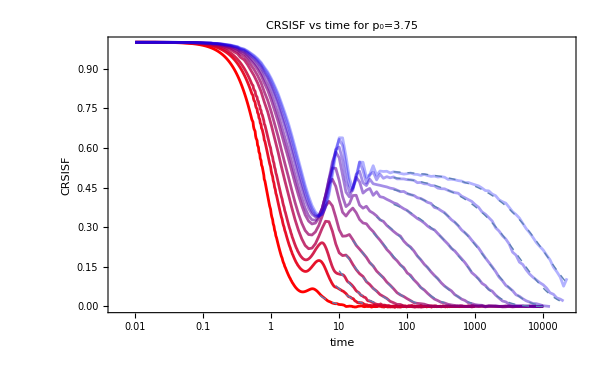
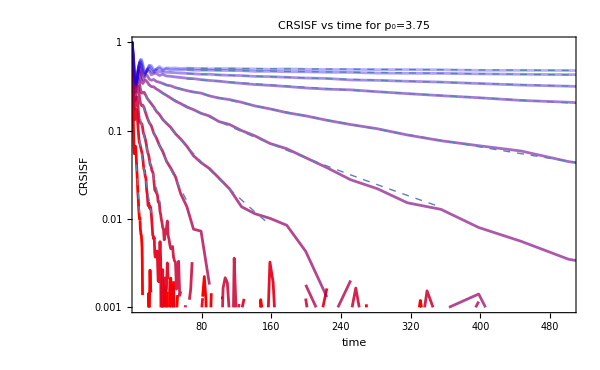
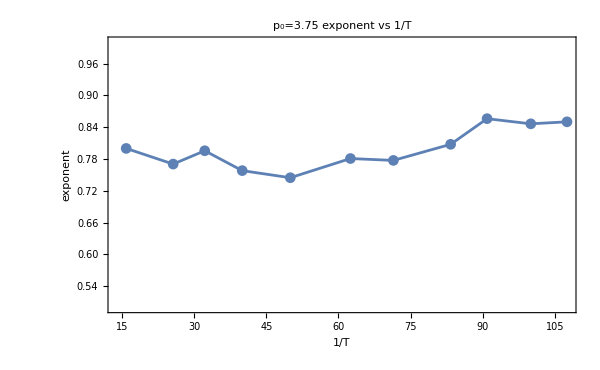
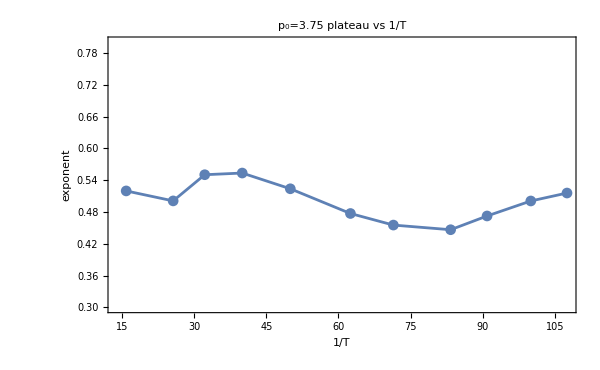
Grid[{-Graphics-,-Graphics-,-Graphics-,-Graphics-},2]

```mathematica
Grid[{Table[Show[
ListLogLinearPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],Table[LogLinearPlot[fits[[1,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick}],{T,Length[temperatures[[p]]]}]],{p,insp,insp}][[1]],Table[Show[
ListLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{10,500},{0.001,1}}],Table[LogPlot[fits[[1,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick}],{T,Length[temperatures[[p]]]}]],{p,insp,insp}][[1]],Table[ListPlot[Table[{1/temperatures[[p,T]],betaSISFfitsTable[[T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" exponent vs 1/T",Joined->True,PlotRange->{All,{0.5,1}}],{p,insp,insp}][[1]],Table[ListPlot[Table[{1/temperatures[[p,T]],plateauSISFfits[[T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" plateau vs 1/T",Joined->True,PlotRange->{All,{0.3,0.8}}],{p,insp,insp}][[1]]},2]
```

```mathematica
fit 3.90
```

```mathematica
fit 3.90
```

#### fit 3.775

```mathematica
insp=5;
```

```mathematica
Length[temperatures[[insp]]]
```

13

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
fitStartNum={{2,10,20,28.98332354454631,43.181917710603976,52.40218049256373,60.75745364744918,300,600,600,1000,1000,1000},{4.746813237004902,9.4598018063875,11.733682063000668,15.866552523746426,18.857083790143243,23.396892354511074,26.06716697056073,28.407935830446753,100,500,500,1000,5000,5000,10000,10000,10000},{4.181227597599696,6.601632624506163,5,7,16.462632220584393,21.83945522645316,21.252851360922705,23.986133137043076,26.71034271282561,28.95468707418388,29.742850824887917,30.967225782497586,34.954383218327905,100,300,300},{5.5443851977847185,8.543302161661563,10.801556831371771,11.484500787075994,14.159855162331585,16.415770244286062,18.57272413948379,22.353104396049027,23.776138167085982,100,500,100,100,100},{12.275005769964972,13.3900602507303,14.607287299171793,18.46868551379298,21.686557895506116,60,60,60,60,60,60,60,60},{5.22625330341219,8.757313686570457,9.787122180079717,11.705078819553803,14.159218058513453,17.924491941701763,19.168324645208596,25.675629384707115,29.712549254051698,31.78020274296657,34.77161632608988}};
```

```mathematica
fitStartPos=Table[Table[Position[absTime[[p,i]],_?(#>fitStartNum[[p,i]]&)][[1,1]],{i,Length[fitStartNum[[p]]]}],{p,Length[p0s]}]
```

{{111,181,211,227,63,65,66,80,86,86,90,90,91},{148,178,187,201,208,58,59,60,70,84,350,380,450,450,481,480,480},{143,162,150,165,202,57,57,58,59,60,60,60,61,281,328,328},{155,174,184,187,196,55,56,57,58,70,84,280,280,281},{189,193,197,56,57,66,66,66,66,66,66,66,66},{152,175,180,52,54,56,56,59,60,61,61}}

```mathematica
fitEndPos=Table[Table[If[AllTrue[CRSISFMean[[p,i]],#>0&],Length[CRSISFMean[[p,i]]],Position[CRSISFMean[[p,i]],_?(#<0.01&)][[1,1]]-1],{i,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{146,212,238,283,78,85,90,100,110,110,112,113,119},{170,214,243,277,293,77,81,88,99,104,468,515,546,554,583,597,617},{151,182,198,232,261,71,73,77,81,85,88,92,98,459,521,554},{163,192,203,215,257,74,79,84,91,99,107,479,509,534},{219,236,259,71,80,87,91,97,101,105,119,119,120},{177,215,232,66,74,81,89,110,108,116,117}}

```mathematica
betaConstrains={0.8>β>0.5,0.8>β>0.5,0.82>β>0.5,0.79>β>0.5,0.78>β>0.7,0.8>β>0.7,0.8>β>0.7,0.8>β>0.7,0.8>β>0.7,0.92>β>0.85,0.92>β>0.88,0.92>β>0.85,0.92>β>0.85}
```

{0.8>β>0.5,0.8>β>0.5,0.82>β>0.5,0.79>β>0.5,0.78>β>0.7,0.8>β>0.7,0.8>β>0.7,0.8>β>0.7,0.8>β>0.7,0.92>β>0.85,0.92>β>0.88,0.92>β>0.85,0.92>β>0.85}

```mathematica
gConstrains={0.52>G>0.3,0.52>G>0.3,0.52>G>0.3,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3};
```

```mathematica
fits=Table[Table[NonlinearModelFit[Table[{Normal[absTime[[p,T]][[rec]]],Normal[CRSISFMean[[p,T,rec]]]},{rec,fitStartPos[[p,T]],fitEndPos[[p,T]]}],{stretchedExp[t,G,τ,β],{betaConstrains[[T]],gConstrains[[T]],50000>τ>0.5}},{{G,0.5},{τ,100},{β,0.8}},t],{T,Length[temperatures[[p]]]}],{p,insp,insp}];
```

```mathematica
fits
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
Length[temperatures[[insp]]]
```

16

```mathematica
plateauSISFfits=Table[fits[[1,T]]["BestFitParameters"][[1,2]],{T,Length[temperatures[[insp]]]}]
```

{0.519743,0.519929,0.493348,0.513299,0.477378,0.464125,0.473343,0.447237,0.466116,0.453748,0.463712,0.480082,0.491375}

```mathematica
betaSISFfitsTable=Table[fits[[1,T]]["BestFitParameters"][[3,2]],{T,Length[temperatures[[insp]]]}]
```

{0.799855,0.799951,0.819766,0.789785,0.779854,0.786847,0.768757,0.778071,0.799953,0.884805,0.880019,0.919951,0.858326}

```mathematica
Table[fits[[1,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[insp]]]}]
```

{4.69287,7.15412,12.9086,23.3229,63.6753,134.467,215.05,530.795,742.094,1380.5,2856.37,7227.75,8665.8}

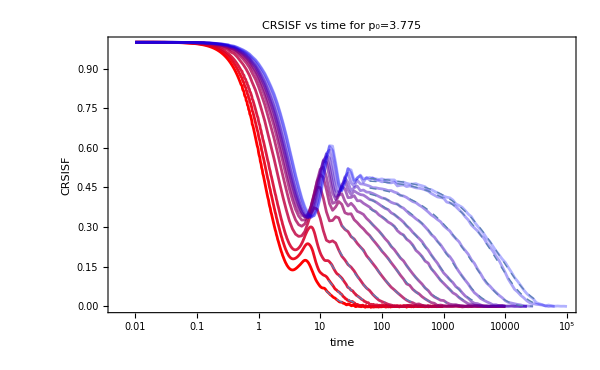
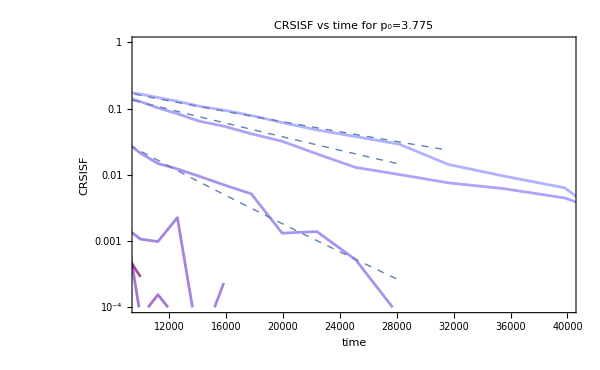
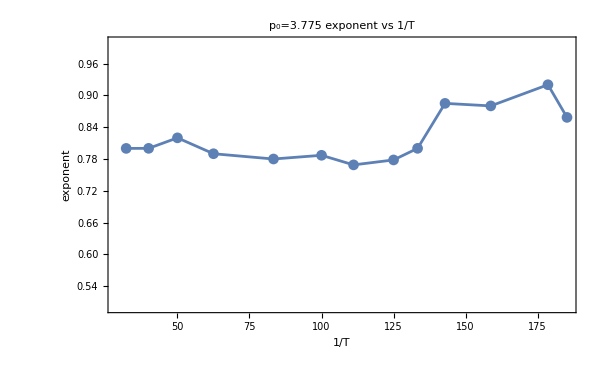
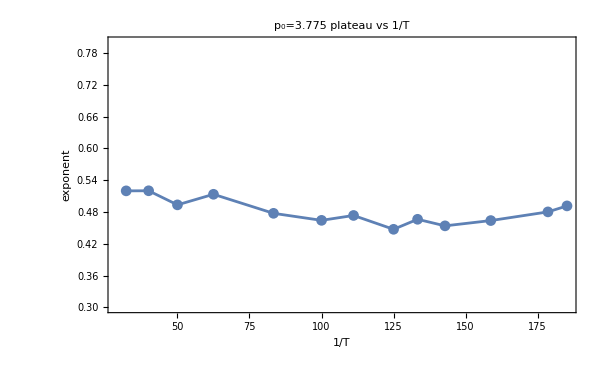
Grid[{-Graphics-,-Graphics-,-Graphics-,-Graphics-},2]

```mathematica
Grid[{Table[Show[
ListLogLinearPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],Table[LogLinearPlot[fits[[1,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick}],{T,Length[temperatures[[p]]]}]],{p,insp,insp}][[1]],Table[Show[
ListLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{10000,40000},{0.0001,1}}],Table[LogPlot[fits[[1,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick}],{T,Length[temperatures[[p]]]}]],{p,insp,insp}][[1]],Table[ListPlot[Table[{1/temperatures[[p,T]],betaSISFfitsTable[[T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" exponent vs 1/T",Joined->True,PlotRange->{All,{0.5,1}}],{p,insp,insp}][[1]],Table[ListPlot[Table[{1/temperatures[[p,T]],plateauSISFfits[[T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" plateau vs 1/T",Joined->True,PlotRange->{All,{0.3,0.8}}],{p,insp,insp}][[1]]},2]
```

```mathematica
fit 3.90
```

```mathematica
fit 3.90
```

#### fit 3.80

```mathematica
insp=4;
```

```mathematica
Length[temperatures[[insp]]]
```

14

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
fitStartNum={{2,10,20,28.98332354454631,43.181917710603976,52.40218049256373,60.75745364744918,300,600,600,1000,1000,1000},{4.746813237004902,9.4598018063875,11.733682063000668,15.866552523746426,18.857083790143243,23.396892354511074,26.06716697056073,28.407935830446753,100,500,500,1000,5000,5000,10000,10000,10000},{4.181227597599696,6.601632624506163,5,7,16.462632220584393,30,35,40,45,60,100,100,100,200,300,300},{5.5443851977847185,8.543302161661563,10.801556831371771,15,20,30,50,60,70,100,100,200,200,200},{12.275005769964972,13.3900602507303,14.607287299171793,18.46868551379298,21.686557895506116,24.53417261923667,25.778256389405044,32.17535373224476,39.18657032041287,41.68125213915501,45.43737491934978,45,45},{5.22625330341219,8.757313686570457,9.787122180079717,11.705078819553803,14.159218058513453,17.924491941701763,19.168324645208596,25.675629384707115,29.712549254051698,31.78020274296657,34.77161632608988}};
```

```mathematica
fitStartPos=Table[Table[Position[absTime[[p,i]],_?(#>fitStartNum[[p,i]]&)][[1,1]],{i,Length[fitStartNum[[p]]]}],{p,Length[p0s]}]
```

{{111,181,211,227,63,65,66,80,86,86,90,90,91},{148,178,187,201,208,58,59,60,70,84,350,380,450,450,481,480,480},{143,162,150,165,202,60,61,63,64,66,70,70,70,311,328,328},{155,174,184,198,211,60,64,66,67,70,71,311,311,311},{189,193,197,56,57,58,59,61,62,63,64,64,64},{152,175,180,52,54,56,56,59,60,61,61}}

```mathematica
fitEndPos=Table[Table[If[AllTrue[CRSISFMean[[p,i]],#>0&],Length[CRSISFMean[[p,i]]],Position[CRSISFMean[[p,i]],_?(#<0.01&)][[1,1]]-1],{i,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{146,212,238,283,78,85,90,100,110,110,112,113,119},{170,214,243,277,293,77,81,88,99,104,468,515,546,554,583,597,617},{151,182,198,232,261,71,73,77,81,85,88,92,98,459,521,554},{163,192,203,215,257,74,79,84,91,99,107,479,509,534},{219,236,259,71,80,87,91,97,101,105,119,119,120},{177,215,232,66,74,81,89,110,108,116,117}}

```mathematica
betaConstrains={0.85>β>0.75,0.81>β>0.75,0.8>β>0.75,0.82>β>0.75,0.805>β>0.75,0.81>β>0.75,0.81>β>0.75,0.81>β>0.75,0.85>β>0.8,0.99>β>0.8,0.99>β>0.75,0.99>β>0.5,0.99>β>0.5,0.99>β>0.85}
```

{0.85>β>0.75,0.81>β>0.75,0.8>β>0.75,0.82>β>0.75,0.805>β>0.75,0.81>β>0.75,0.81>β>0.75,0.81>β>0.75,0.85>β>0.8,0.99>β>0.8,0.99>β>0.75,0.99>β>0.5,0.99>β>0.5,0.99>β>0.85}

```mathematica
gConstrains={0.55>G>0.45,0.55>G>0.45,0.5>G>0.4,0.48>G>0.3,0.48>G>0.3,0.48>G>0.3,0.48>G>0.3,0.48>G>0.3,0.48>G>0.4,0.48>G>0.4,0.48>G>0.4,0.48>G>0.4,0.48>G>0.4,0.48>G>0.4};
```

```mathematica
fits=Table[Table[NonlinearModelFit[Table[{Normal[absTime[[p,T]][[rec]]],Normal[CRSISFMean[[p,T,rec]]]},{rec,fitStartPos[[p,T]],fitEndPos[[p,T]]}],{stretchedExp[t,G,τ,β],{betaConstrains[[T]],gConstrains[[T]],tauConstraints[[T]]}},{{G},{τ},{β}},t],{T,Length[temperatures[[p]]]}],{p,insp,insp}];
```

```mathematica
fits
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
tauConstraints=Table[10^(Log10[tauCRSISFfits[[i]]]+0.2)>τ&&τ>10^(Log10[tauCRSISFfits[[i]]]-0.2),{i,Length[temperatures[[insp]]]}]
```

{2.35962>τ&&τ>0.939382,4.09851>τ&&τ>1.63165,4.79669>τ&&τ>1.9096,6.36909>τ&&τ>2.53558,17.914>τ&&τ>7.13171,54.9526>τ&&τ>21.877,93.4061>τ&&τ>37.1856,178.768>τ&&τ>71.1689,402.218>τ&&τ>160.126,942.238>τ&&τ>375.112,2584.83>τ&&τ>1029.04,4382.58>τ&&τ>1744.74,8203.36>τ&&τ>3265.82,13065.4>τ&&τ>5201.43}

```mathematica
tauCRSISFfits=Table[fits[[1,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[insp]]]}]
```

{1.48882,2.58599,3.02651,4.01862,11.303,34.6727,58.9353,112.795,253.783,594.512,1630.92,2765.22,5175.97,8243.71}

```mathematica
Length[temperatures[[insp]]]
```

16

```mathematica
plateauSISFfits=Table[fits[[1,T]]["BestFitParameters"][[1,2]],{T,Length[temperatures[[insp]]]}]
```

{0.465605,0.451177,0.497475,0.479511,0.479931,0.479949,0.479831,0.479773,0.465097,0.444067,0.44673,0.415044,0.417532,0.435667}

```mathematica
betaSISFfitsTable=Table[fits[[1,T]]["BestFitParameters"][[3,2]],{T,Length[temperatures[[insp]]]}]
```

{0.765941,0.750626,0.798784,0.819717,0.804949,0.809946,0.809883,0.809918,0.800227,0.800043,0.793912,0.98495,0.976405,0.888681}

```mathematica
{0.9225667337378314,0.6002981301973063,0.7741797546838524,0.6659184479828183,0.6833542857528847,0.6321256056354989,0.6571634958147435,0.7198166404594938,0.7199209846252685,0.7198211712453488,0.715022209850623,0.7199262016115247,0.6980841985138433}
```

{0.922567,0.600298,0.77418,0.665918,0.683354,0.632126,0.657163,0.719817,0.719921,0.719821,0.715022,0.719926,0.698084}

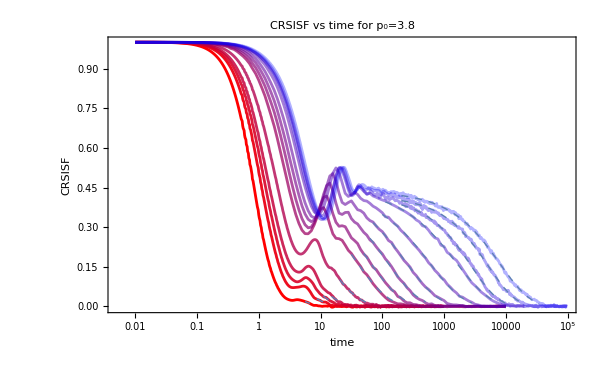
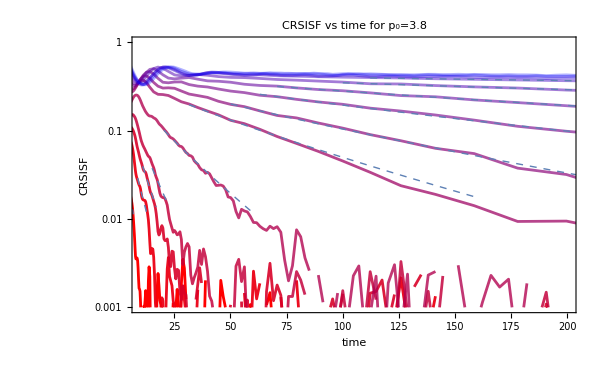
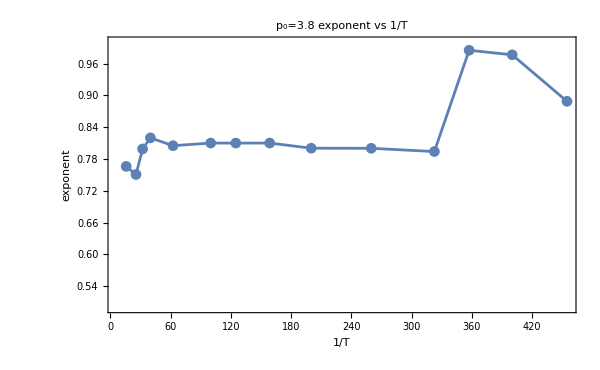
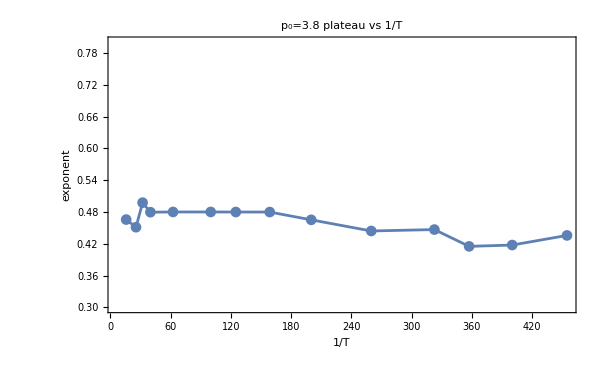
Grid[{-Graphics-,-Graphics-,-Graphics-,-Graphics-},2]

```mathematica
Grid[{Table[Show[
ListLogLinearPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],Table[LogLinearPlot[fits[[1,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick}],{T,Length[temperatures[[p]]]}]],{p,insp,insp}][[1]],Table[Show[
ListLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{10,200},{0.001,1}}],Table[LogPlot[fits[[1,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick}],{T,Length[temperatures[[p]]]}]],{p,insp,insp}][[1]],Table[ListPlot[Table[{1/temperatures[[p,T]],betaSISFfitsTable[[T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" exponent vs 1/T",Joined->True,PlotRange->{All,{0.5,1}}],{p,insp,insp}][[1]],Table[ListPlot[Table[{1/temperatures[[p,T]],plateauSISFfits[[T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" plateau vs 1/T",Joined->True,PlotRange->{All,{0.3,0.8}}],{p,insp,insp}][[1]]},2]
```

```mathematica
fit 3.90
```

```mathematica
fit 3.90
```

#### Summary

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
fitStartNum={{2,10,20,28.98332354454631,60,80,100,300,600,600,1000,1000,1000},{4.746813237004902,9.4598018063875,11.733682063000668,15.866552523746426,18.857083790143243,23.396892354511074,26.06716697056073,28.407935830446753,100,500,500,1000,5000,5000,10000,10000,10000},{4.181227597599696,6.601632624506163,5,7,16.462632220584393,30,35,40,45,60,100,100,100,200,300,300},{5.5443851977847185,8.543302161661563,10.801556831371771,15,20,30,50,60,70,100,100,200,200,200},{12.275005769964972,13.3900602507303,14.607287299171793,18.46868551379298,21.686557895506116,60,60,60,60,60,60,60,60},{5.22625330341219,8.757313686570457,9.787122180079717,11.705078819553803,14.159218058513453,30,35,60,60,60,60}};
```

```mathematica
fitEndPosNum={10^-2.5,10^-2.5,0.01,0.01,0.01,0.01};
```

```mathematica
fitStartPos=Table[Table[Position[absTime[[p,i]],_?(#>fitStartNum[[p,i]]&)][[1,1]],{i,Length[fitStartNum[[p]]]}],{p,Length[p0s]}]
```

{{111,181,211,227,66,69,70,80,86,86,90,90,91},{148,178,187,201,208,58,59,60,70,84,350,380,450,450,481,480,480},{143,162,150,165,202,60,61,63,64,66,70,70,70,311,328,328},{155,174,184,198,211,60,64,66,67,70,71,311,311,311},{189,193,197,56,57,66,66,66,66,66,66,66,66},{152,175,180,52,54,60,61,66,66,66,66}}

```mathematica
fitEndPos=Table[Table[If[AllTrue[CRSISFMean[[p,i]],#>0&],Length[CRSISFMean[[p,i]]],Position[CRSISFMean[[p,i]],_?(#<fitEndPosNum[[p]]&)][[1,1]]-1],{i,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{155,218,245,295,81,87,93,104,110,110,112,113,119},{188,228,252,294,298,80,82,90,102,106,474,527,558,560,596,605,624},{151,182,198,232,261,71,73,77,81,85,88,92,98,459,521,554},{163,192,203,215,257,74,79,84,91,99,107,479,509,534},{219,236,259,71,80,87,91,97,101,105,119,119,120},{177,215,232,66,74,81,89,110,108,116,117}}

```mathematica
betaConstrains={{0.99>β>0.5,0.999>β>0.78,0.8>β>0.75,0.999>β>0.73,0.999>β>0.75,0.999>β>0.75,0.8>β>0.75,0.8>β>0.75,0.75>β>0.65,0.8>β>0.75,0.75>β>0.55,0.78>β>0.75,0.75>β>0.55},{0.85>β>0.8,0.85>β>0.8,0.85>β>0.75,0.85>β>0.75,0.85>β>0.8,0.85>β>0.8,0.85>β>0.8,0.85>β>0.8,0.85>β>0.8,0.85>β>0.8,0.85>β>0.8,0.85>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.5,0.99>β>0.8},{0.999>β>0.9,0.999>β>0.9,0.999>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.9,0.95>β>0.7,0.95>β>0.7,0.95>β>0.8,0.95>β>0.6,0.95>β>0.6,0.95>β>0.6},{0.85>β>0.75,0.88>β>0.83,0.8>β>0.75,0.82>β>0.75,0.805>β>0.75,0.81>β>0.75,0.81>β>0.75,0.81>β>0.75,0.85>β>0.8,0.99>β>0.8,0.99>β>0.75,0.99>β>0.5,0.99>β>0.5,0.99>β>0.85},{0.8>β>0.5,0.8>β>0.5,0.82>β>0.5,0.79>β>0.5,0.78>β>0.7,0.8>β>0.7,0.8>β>0.7,0.8>β>0.7,0.8>β>0.7,0.92>β>0.85,0.92>β>0.88,0.92>β>0.85,0.92>β>0.85},{0.77>β>0.5,0.77>β>0.74,0.77>β>0.5,0.99>β>0.5,0.99>β>0.6,0.99>β>0.6,0.99>β>0.75,0.9>β>0.68,0.99>β>0.6,0.99>β>0.6,0.85>β>0.6}};
```

```mathematica
gConstrains={{0.99>G>0.6,0.75>G>0.65,0.70>G>0.60,0.9>G>0.68,0.9>G>0.68,0.9>G>0.66,0.7>G>0.3,0.99>G>0.4,0.99>G>0.4,0.99>G>0.4,0.99>G>0.4,0.99>G>0.4,0.99>G>0.4},{0.52>G>0.48,0.52>G>0.48,0.48>G>0.4,0.48>G>0.4,0.48>G>0.4,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3,0.99>G>0.3},{0.44>G>0.38,0.44>G>0.38,0.44>G>0.38,0.44>G>0.38,0.44>G>0.38,0.44>G>0.38,0.44>G>0.38,0.44>G>0.38,0.44>G>0.38,0.42>G>0.38,0.42>G>0.38,0.42>G>0.38,0.42>G>0.38,0.5>G>0.3,0.5>G>0.3,0.5>G>0.3},{0.65>G>0.555,0.65>G>0.55,0.58>G>0.55,0.55>G>0.3,0.55>G>0.3,0.55>G>0.3,0.55>G>0.3,0.55>G>0.3,0.55>G>0.4,0.55>G>0.4,0.55>G>0.4,0.55>G>0.4,0.48>G>0.4,0.48>G>0.4},{0.6>G>0.48,0.6>G>0.48,0.6>G>0.52,0.8>G>0.45,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3,0.8>G>0.3},{0.7>G>0.5,0.8>G>0.6,0.8>G>0.55,0.99>G>0.3,0.99>G>0.5,0.99>G>0.5,0.6>G>0.4,0.6>G>0.4,0.6>G>0.4,0.6>G>0.4,0.6>G>0.4}};
```

```mathematica
fits=Table[Table[NonlinearModelFit[Table[{Normal[absTime[[p,T]][[rec]]],Normal[CRSISFMean[[p,T,rec]]]},{rec,fitStartPos[[p,T]],fitEndPos[[p,T]]}],{stretchedExp[t,G,τ,β],{betaConstrains[[p,T]],gConstrains[[p,T]],50000>τ>0.5}},{{G},{τ},{β}},t],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
plateauSISFfits=Table[Table[Around[fits[[p,T]]["BestFitParameters"][[1,2]],fits[[p,T]]["ParameterErrors"][[1]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{{1.00.8,0.71.1,0.70.5,0.680.15,0.680.24,0.660.06,0.6210.030,0.6360.016,0.6760.034,0.6640.021,0.7010.025,0.6750.014,0.7390.018},{0.51.1,0.520.18,0.480.09,0.4800.029,0.4800.021,0.5090.031,0.4710.014,0.4710.006,0.4860.006,0.4460.012,0.4740.008,0.4920.005,0.4480.010,0.4840.009,0.4700.009,0.4780.007,0.5000.005},{0.12.,0.40.9,0.40.4,0.400.06,0.3800.030,0.440.08,0.420.05,0.4380.028,0.4100.019,0.4200.015,0.3890.015,0.4190.008,0.4200.005,0.4350.005,0.40880.0025,0.39900.0010},{0.8.,0.63.5,0.61.5,0.53.3,0.540.11,0.520.07,0.490.07,0.4820.035,0.4650.009,0.4440.007,0.4470.004,0.41500.0019,0.41750.0014,0.43570.0011},{0.600.32,0.600.13,0.520.05,0.510.08,0.4770.010,0.4640.014,0.4730.008,0.4470.005,0.4660.004,0.45370.0025,0.46370.0020,0.48010.0018,0.49140.0011},{0.71.4,0.60.4,0.580.17,0.550.08,0.5240.025,0.5000.026,0.4550.006,0.4460.004,0.47240.0016,0.50070.0028,0.51570.0022}}

```mathematica
fits[[1,1]]["ParameterErrors"]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{0.828542,0.630174,0.302419}

```mathematica
betaSISFfitsTable=Table[Table[Around[fits[[p,T]]["BestFitParameters"][[3,2]],fits[[p,T]]["ParameterErrors"][[3]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{{0.990.30,0.80.4,0.800.17,0.730.07,0.750.13,0.750.05,0.7500.030,0.7590.016,0.7500.028,0.7530.020,0.7160.021,0.7700.016,0.6980.016},{0.80.5,0.850.12,0.850.08,0.850.04,0.8340.028,0.800.04,0.8430.026,0.8500.017,0.8000.013,0.8500.022,0.8040.014,0.7780.009,0.8360.017,0.8290.014,0.8600.015,0.8120.013,0.8000.011},{0.8.,0.90.7,0.90.4,0.950.11,0.930.05,0.930.10,0.950.09,0.910.04,0.900.04,0.9330.034,0.950.04,0.9200.021,0.9030.016,0.7690.012,0.7220.008,0.7720.005},{0.83.0,0.81.6,0.80.7,0.81.6,0.800.07,0.810.07,0.810.08,0.810.05,0.8000.017,0.8000.017,0.7940.013,0.9850.011,0.9760.009,0.8890.006},{0.800.15,0.800.07,0.800.04,0.790.08,0.7800.017,0.7870.022,0.7690.014,0.7780.014,0.8000.011,0.8850.012,0.8800.011,0.9200.013,0.8580.007},{0.80.4,0.740.21,0.770.11,0.760.06,0.7440.027,0.7490.034,0.7770.014,0.8080.014,0.8560.007,0.8460.015,0.8500.016}}

```mathematica
tauSISFfitsTable=Table[Table[Around[fits[[p,T]]["BestFitParameters"][[2,2]],fits[[p,T]]["ParameterErrors"][[2]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{{1.00.6,3.4.,7.4.,15.4.,40.17.,101.12.,182.12.,580.21.,963.66.,1237.56.,1919.100.,2675.79.,3164.122.},{1.42.6,4.71.5,8.91.7,20.91.5,28.01.5,48.4.,74.63.0,193.4.,557.10.,1213.42.,1622.37.,3978.63.,9873.290.,11781.280.,23989.576.,31681.689.,44007.721.},{1.24.,2.4.,3.22.8,9.01.5,18.51.6,27.5.,41.5.,56.4.,95.5.,136.6.,227.11.,303.8.,563.9.,1282.23.,4711.52.,11491.61.},{1.13.,2.12.,3.7.,5.24.,11.02.2,34.6.,58.10.,113.11.,234.7.,586.14.,1595.24.,2763.19.,5176.32.,8093.40.},{4.42.1,6.61.4,12.21.3,23.5.,63.72.0,134.6.,215.5.,531.9.,742.10.,1380.13.,2856.27.,7228.72.,8666.55.},{1.42.3,3.52.6,6.22.0,11.92.0,23.71.6,65.5.,170.4.,693.11.,1497.9.,4466.59.,11419.141.}}

```mathematica
calibrationT={10,10,14,11,10,8};
```

```mathematica
fitsPlots=Table[Show[
ListLogLinearPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],Table[LogLinearPlot[fits[[p,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotStyle->{Dashed,Thick,Black}],{T,Length[temperatures[[p]]]}]],{p,1,Length[p0s]}]
```

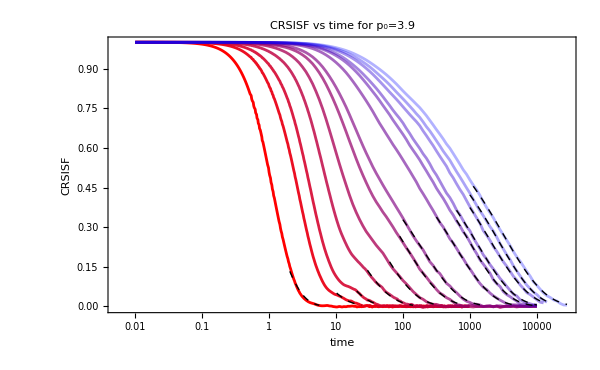
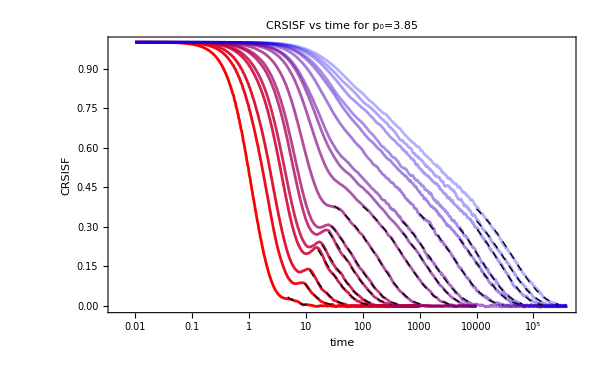
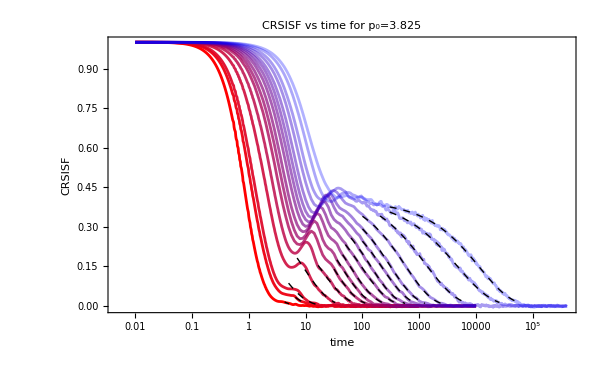
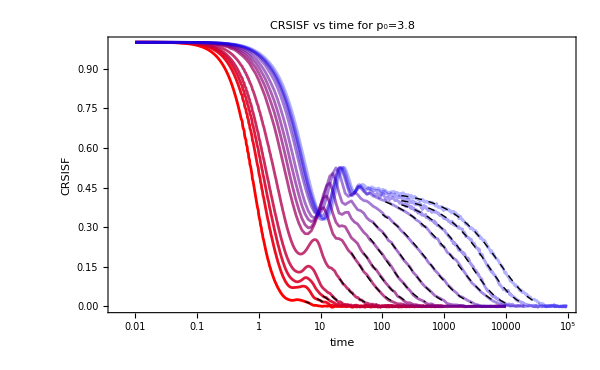
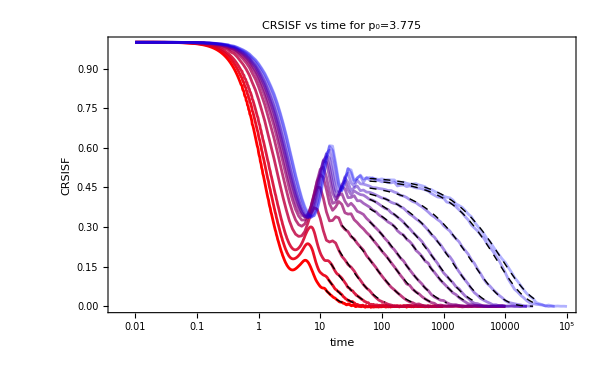
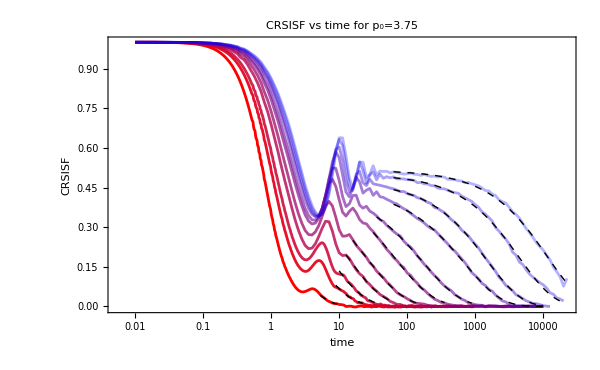

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
✓×
```

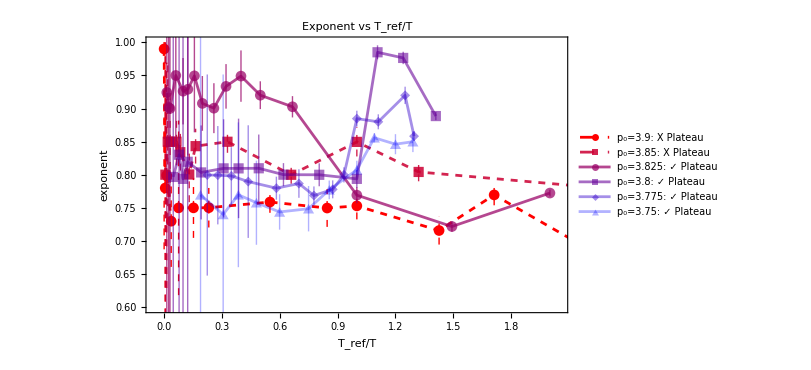

```mathematica
exponentPlot=Show[ListPlot[Table[Table[{temperatures[[p,calibrationT[[p]]]]/temperatures[[p,T]],betaSISFfitsTable[[p,T]]},{T,Length[temperatures[[p]]]}],{p,1,2}],PlotMarkers->Automatic,FrameLabel->{"T_ref/T","exponent"},ImageSize->600,PlotLabel->"Exponent vs T_ref/T",Joined->True,PlotRange->{{-0.05,2.05},{0.6,1.0}},PlotStyle->{{Dashed,redBluePlotConfig[6][[1]]},{Dashed,redBluePlotConfig[6][[2]]}},PlotLegends->Table["p_0="<>ToString[p0s[[p]]]<>": X Plateau",{p,2}]],ListPlot[Table[Table[{temperatures[[p,calibrationT[[p]]]]/temperatures[[p,T]],betaSISFfitsTable[[p,T]]},{T,Length[temperatures[[p]]]}],{p,3,Length[p0s]}],PlotMarkers->Automatic,FrameLabel->{"T_ref/T","exponent"},ImageSize->600,PlotLabel->"Exponent vs T_ref/T",Joined->True,PlotRange->{{0,2},{0.6,1.0}},PlotStyle->redBluePlotConfig[6][[3;;]],PlotLegends->Table["p_0="<>ToString[p0s[[p]]]<>": ✓ Plateau",{p,3,Length[p0s]}]]]
```

```mathematica
Directive
```

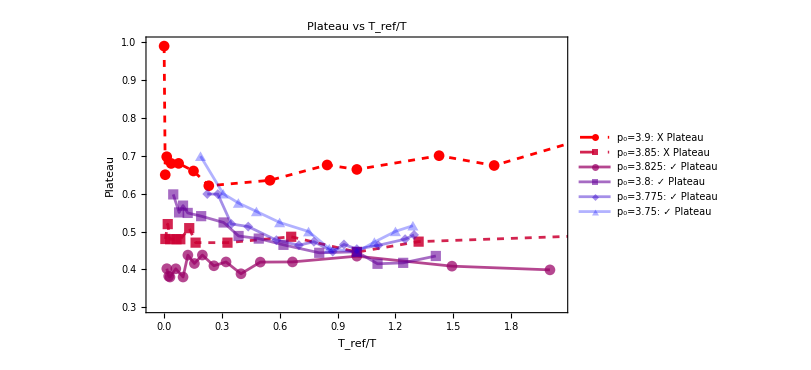

```mathematica
plateauPlot=Show[ListPlot[Table[Table[{temperatures[[p,calibrationT[[p]]]]/temperatures[[p,T]],plateauSISFfits[[p,T]]},{T,Length[temperatures[[p]]]}],{p,1,2}],PlotMarkers->Automatic,FrameLabel->{"T_ref/T","Plateau"},ImageSize->600,PlotLabel->"Plateau vs T_ref/T",Joined->True,PlotRange->{{-0.05,2.05},{0.3,1.0}},PlotStyle->{{Dashed,redBluePlotConfig[6][[1]]},{Dashed,redBluePlotConfig[6][[2]]}},PlotLegends->Table["p_0="<>ToString[p0s[[p]]]<>": X Plateau",{p,2}]],ListPlot[Table[Table[{temperatures[[p,calibrationT[[p]]]]/temperatures[[p,T]],plateauSISFfits[[p,T]]},{T,Length[temperatures[[p]]]}],{p,3,Length[p0s]}],PlotMarkers->Automatic,FrameLabel->{"T_ref/T","Plateau"},ImageSize->600,PlotLabel->"Plateau vs T_ref/T",Joined->True,PlotRange->{{-0.1,2},{0.3,1.0}},PlotStyle->redBluePlotConfig[6][[3;;]],PlotLegends->Table["p_0="<>ToString[p0s[[p]]]<>": ✓ Plateau",{p,3,Length[p0s]}]]]
```

```mathematica
τ
```

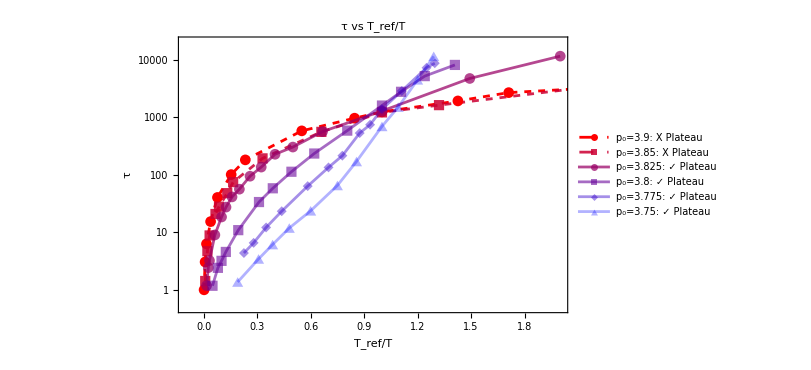

```mathematica
tauPlot=Show[ListLogPlot[Table[Table[{temperatures[[p,calibrationT[[p]]]]/temperatures[[p,T]],tauSISFfitsTable[[p,T]]},{T,Length[temperatures[[p]]]}],{p,1,2}],PlotMarkers->Automatic,FrameLabel->{"T_ref/T","τ"},ImageSize->600,PlotLabel->"τ vs T_ref/T",Joined->True,PlotRange->{{-0.1,2},{0.5,20000}},PlotStyle->{{Dashed,redBluePlotConfig[6][[1]]},{Dashed,redBluePlotConfig[6][[2]]}},PlotLegends->Table["p_0="<>ToString[p0s[[p]]]<>": X Plateau",{p,2}]],ListLogPlot[Table[Table[{temperatures[[p,calibrationT[[p]]]]/temperatures[[p,T]],tauSISFfitsTable[[p,T]]},{T,Length[temperatures[[p]]]}],{p,3,Length[p0s]}],PlotMarkers->Automatic,FrameLabel->{"T_ref/T","Plateau"},ImageSize->600,PlotLabel->"Plateau vs T_ref/T",Joined->True,PlotRange->{{-0.1,10},All},PlotStyle->redBluePlotConfig[6][[3;;]],PlotLegends->Table["p_0="<>ToString[p0s[[p]]]<>": ✓ Plateau",{p,3,Length[p0s]}]]]
```

```mathematica
plateauErrorBar=Table[ListLogLinearPlot[Table[{1/temperatures[[p,T]],plateauSISFfits[[p,T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","Plateau"},ImageSize->600,PlotLabel->"Plateau vs 1/T for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{All,{0,1}}],{p,Length[p0s]}];
```

```mathematica
exponentErrorBar=Table[ListLogLinearPlot[Table[{1/temperatures[[p,T]],betaSISFfitsTable[[p,T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","Exponent"},ImageSize->600,PlotLabel->"Exponent vs 1/T for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{All,{0,1}}],{p,Length[p0s]}];
```

```mathematica
Table[Export["/home/chengling/Research/updates/06102024/erroBars"<>ToString[p0s[[p]]]<>".jpeg",Grid[Partition[{exponentErrorBar[[p]],plateauErrorBar[[p]]},1]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/06102024/erroBars3.9.jpeg,/home/chengling/Research/updates/06102024/erroBars3.85.jpeg,/home/chengling/Research/updates/06102024/erroBars3.825.jpeg,/home/chengling/Research/updates/06102024/erroBars3.8.jpeg,/home/chengling/Research/updates/06102024/erroBars3.775.jpeg,/home/chengling/Research/updates/06102024/erroBars3.75.jpeg}

```mathematica
Export["/home/chengling/Research/updates/06102024/fittingResults.jpeg",Grid[Partition[{tauPlot,exponentPlot,plateauPlot},1]],ImageResolution->800]
```

/home/chengling/Research/updates/06102024/fittingResults.jpeg

```mathematica
Export["/home/chengling/Research/updates/06102024/CRSISF.jpeg",Grid[Partition[Table[fitsPlots[[p]],{p,Length[p0s]}],2]],ImageResolution->800]
```

/home/chengling/Research/updates/06102024/CRSISF.jpeg

### get CRoverlap

```mathematica
tauCRoverlap={{5.467779297575122,20.613642606152737,41.17750526883994,114.29382075758781,286.43511505989983,678.2646368626888,1169.103208345351,3718.27122133873,6706.364317175721,8804.932989716244,13703.91538162604,16808.419219535594,25000.057718467295},{7.834976775992932,22.460497359787702,40.922793734483406,94.78280185436874,128.79453931137476,231.55461796962314,323.17926259327726,843.8681996277791,2586.1167985909237,5036.916402039757,7314.717671434624,18600.880936529808,40307.93498223004,52624.590535830495,98462.79050610549,139254.67185534368,202268.02162912188},{4.908732268246582,9.31848873794692,13.186591725727347,32.26259187830922,66.35481014996512,100.38226732553892,143.960577154809,209.23274864109732,333.8968037849868,460.04501744315485,668.6308529783303,958.8992763643564,1725.6436531887025,4336.275018528646,13857.138919303605,33009.675825311846},{5.833319418117253,11.86278894161065,16.917338892978847,23.25548620200179,52.160702899712064,144.03673884723923,226.53383746332744,388.1550799983505,724.5750497347012,1566.498812260033,3781.0544591126413,5197.718904387892,9467.910598016313,16829.017670811918},{21.619985749005966,32.80814949132081,54.24988005944357,95.37884407734762,214.3138451376967,390.9176109117116,607.9474733218694,1179.063759260535,1641.9990713125321,2617.0270956732875,5138.149035368009,12125.896327499202,16276.75146370977},{7.902412047505973,19.283025782079278,31.495641101457004,56.8726382139789,102.69945793602908,219.20701228447996,462.71746977000464,1364.7589278528767,2755.0853906568686,8309.108378539784,18544.838218136134}};
```

### tauAlphaTable

```mathematica
tauAlphafitingPlot=Table[ListLogPlot[{Table[{1/temperatures[[p,T]],tauSISFfitsTable[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{1/temperatures[[p,T]],tauCRoverlap[[p,T]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"1/T","τα"},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" τα vs 1/T",Joined->True,PlotRange->All],{p,Length[p0s]}];
```

```mathematica
Table[Export["/home/chengling/Research/updates/06102024/fitting"<>ToString[p0s[[p]]]<>".jpeg",Grid[Partition[{fitsPlots[[p]],tauAlphafitingPlot[[p]],ListPlot[Table[{temperatures[[p,calibrationT[[p]]]]/temperatures[[p,T]],betaSISFfitsTable[[p,T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"Exponent vs 1/T",Joined->True,PlotRange->{All,{0.3,1}}],ListPlot[Table[{temperatures[[p,calibrationT[[p]]]]/temperatures[[p,T]],plateauSISFfits[[p,T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","plateau"},ImageSize->600,PlotLabel->"Plateau vs 1/T",Joined->True,PlotRange->{All,{0.3,1}}]},2]],ImageResolution->800],{p,Length[p0s]}];
```

```mathematica
tauAlphaTable=Table[Prepend[Table[{temperatures[[p,T]],tauCRSISFfits[[p,T]],tauCRoverlap[[p,T]]},{T,Length[temperatures[[p]]]}],{"T","τ by fitting CRSISF","τ when CRoverlap=1/e"}],{p,Length[p0s]}]
```

{{{T,τ by fitting CRSISF,τ when CRoverlap=1/e},{0.039,0.917578,5.46778},{0.01,6.41115,20.6136},{0.005,10.17,41.1775},{0.002,30.8586,114.294},{0.001,59.937,286.435},{0.0005,113.194,678.265},{0.00033,140.946,1169.1},{0.00014,635.695,3718.27},{0.000091,1084.9,6706.36},{0.000077,1109.59,8804.93},{0.000054,1484.94,13703.9},{0.000045,2034.22,16808.4},{0.000036,2499.28,25000.1}},{{T,τ by fitting CRSISF,τ when CRoverlap=1/e},{0.039,3.10178,7.83498},{0.016,5.53581,22.4605},{0.01,6.0405,40.9228},{0.005,14.3715,94.7828},{0.00385,26.6191,128.795},{0.0025,46.6258,231.555},{0.002,75.9876,323.179},{0.001,198.8,843.868},{0.0005,534.267,2586.12},{0.00033,1296.6,5036.92},{0.00025,2170.76,7314.72},{0.00014,3986.38,18600.9},{0.000091,9994.46,40307.9},{0.000077,15655.4,52624.6},{0.000054,24221.6,98462.8},{0.000045,31978.6,139255.},{0.000036,40190.1,202268.}},{{T,τ by fitting CRSISF,τ when CRoverlap=1/e},{0.063,2.11057,4.90873},{0.039,2.85356,9.31849},{0.03105,4.87734,13.1866},{0.016,9.57941,32.2626},{0.01,20.3168,66.3548},{0.008,31.3789,100.382},{0.0063,43.8563,143.961},{0.005,58.3188,209.233},{0.00385,88.3965,333.897},{0.0031,128.237,460.045},{0.0025,181.52,668.631},{0.002,263.171,958.899},{0.0015,475.008,1725.64},{0.001,1196.59,4336.28},{0.00067,4927.94,13857.1},{0.0005,11647.,33009.7}},{{T,τ by fitting CRSISF,τ when CRoverlap=1/e},{0.063,1.48287,5.83332},{0.039,3.82569,11.8628},{0.03105,4.89304,16.9173},{0.025,6.38523,23.2555},{0.016,14.242,52.1607},{0.01,46.5344,144.037},{0.008,66.0874,226.534},{0.0063,123.706,388.155},{0.005,224.162,724.575},{0.00385,540.572,1566.5},{0.0031,1792.47,3781.05},{0.0028,2629.31,5197.72},{0.0025,4961.05,9467.91},{0.0022,7943.29,16829.}},{{T,τ by fitting CRSISF,τ when CRoverlap=1/e},{0.03105,6.61161,21.62},{0.025,9.85835,32.8081},{0.02,17.0235,54.2499},{0.016,32.58,95.3788},{0.012,68.8304,214.314},{0.01,130.877,390.918},{0.009,206.511,607.947},{0.008,494.14,1179.06},{0.0075,741.541,1642.},{0.007,1363.85,2617.03},{0.0063,2787.39,5138.15},{0.0056,7222.68,12125.9},{0.0054,8656.99,16276.8}},{{T,τ by fitting CRSISF,τ when CRoverlap=1/e},{0.063,1.25046,7.90241},{0.039,6.66694,19.283},{0.03105,9.80135,31.4956},{0.025,14.2196,56.8726},{0.02,23.6898,102.699},{0.016,68.062,219.207},{0.014,161.418,462.717},{0.012,632.614,1364.76},{0.011,1472.07,2755.09},{0.01,4476.39,8309.11},{0.0093,11364.6,18544.8}}}

```mathematica
Table[Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP"<>ToString[NumberForm[p0s[[p]],{5,3}]]<>".csv",tauAlphaTable[[p]],"CSV"],{p,Length[p0s]}]
```

{/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.900.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.850.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.825.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.800.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.775.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.750.csv}

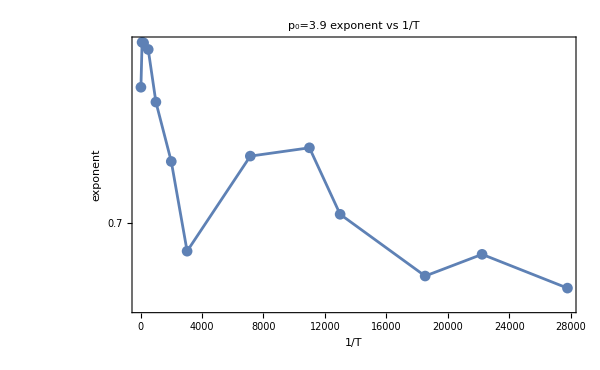
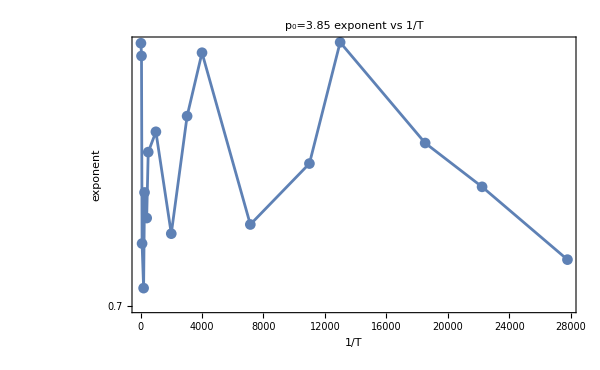
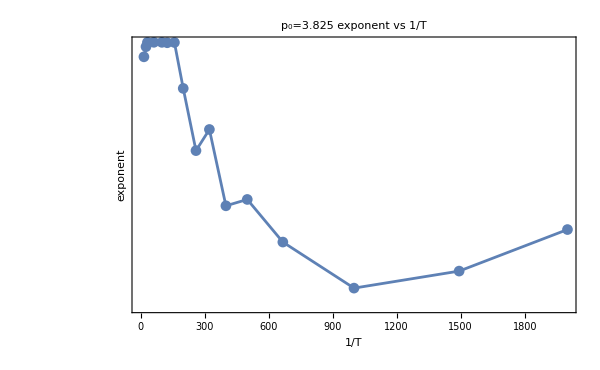
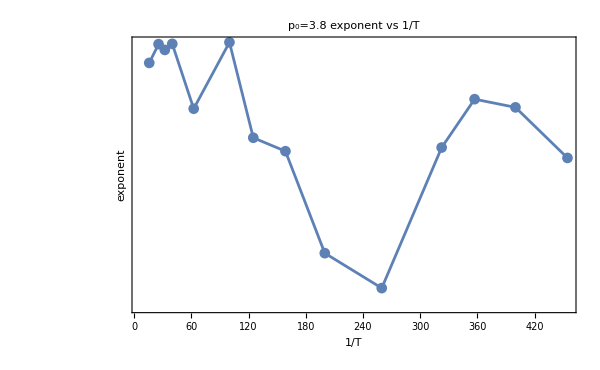
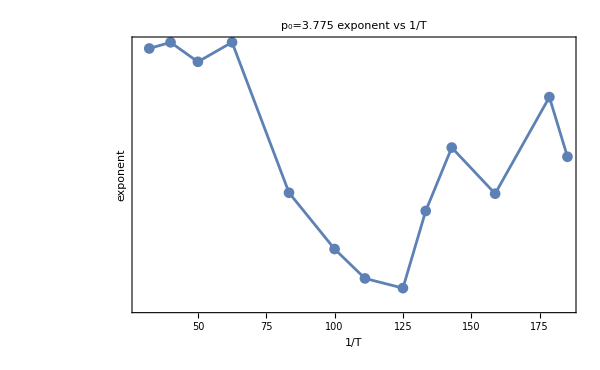
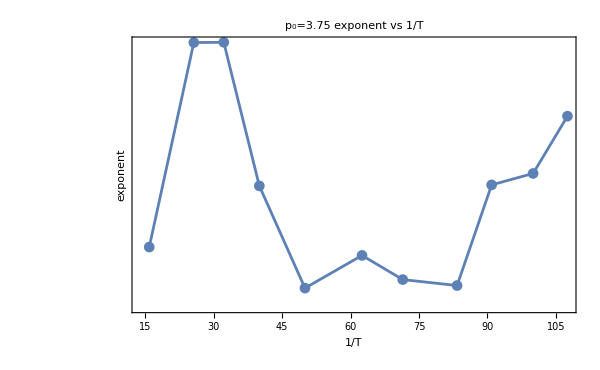

```mathematica
exponentPlots=Table[ListLogPlot[Table[{1/temperatures[[p,T]],betaSISFfitsTable[[p,T]]},{T,Length[temperatures[[p]]]}],PlotMarkers->Automatic,FrameLabel->{"1/T","exponent"},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" exponent vs 1/T",Joined->True,PlotRange->All],{p,Length[p0s]}]
```

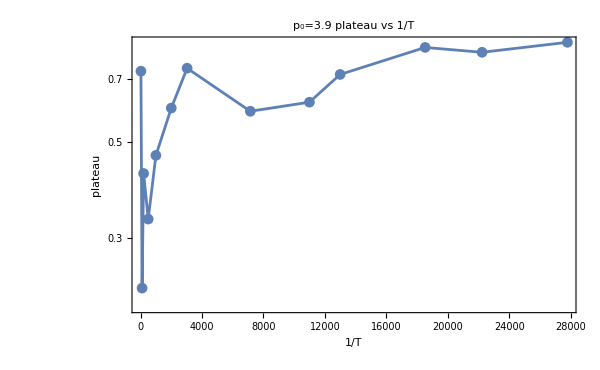
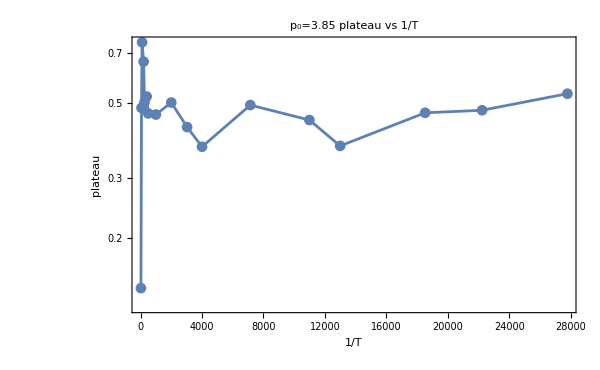
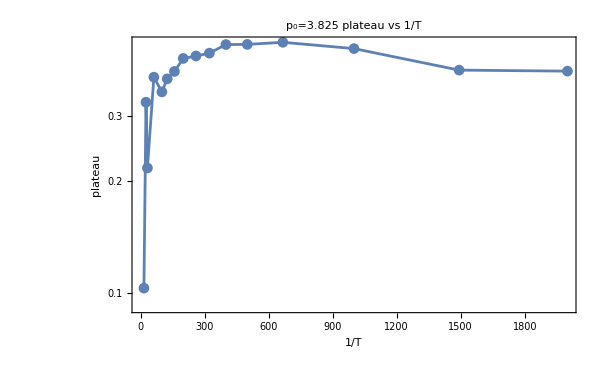
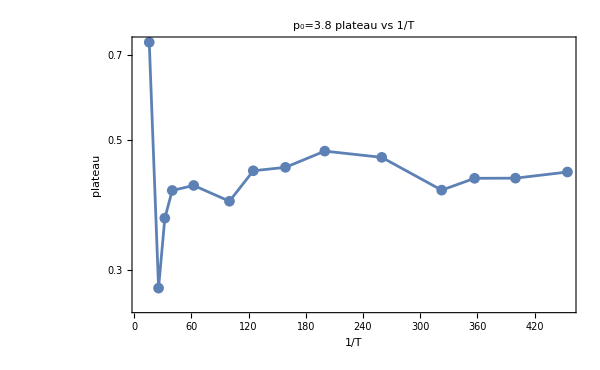
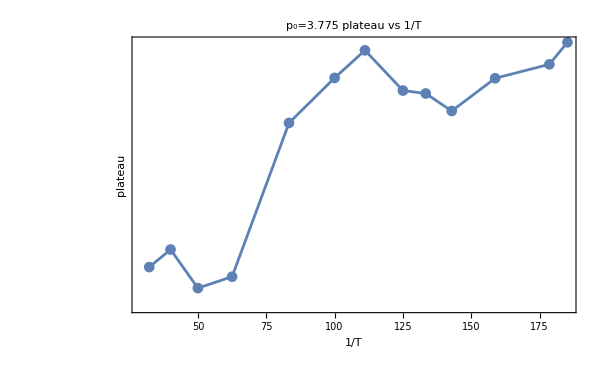
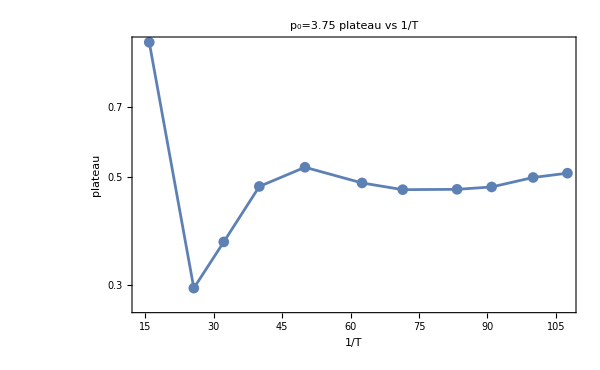

```mathematica
plateauPlots=Table[ListLogPlot[Table[{1/temperatures[[p,T]],plateauSISFfits[[p,T]]},{T,Length[temperatures[[p]]]}],FrameLabel->{"1/T","plateau"},PlotMarkers->Automatic,ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" plateau vs 1/T",Joined->True,PlotRange->All],{p,Length[p0s]}]
```

```mathematica
results=Table[Grid[Partition[{CRSISFFittingPlots[[p]],tauAlphafitingPlot[[p]],plateauPlots[[p]],exponentPlots[[p]]},2]],{p,Length[p0s]}];
```

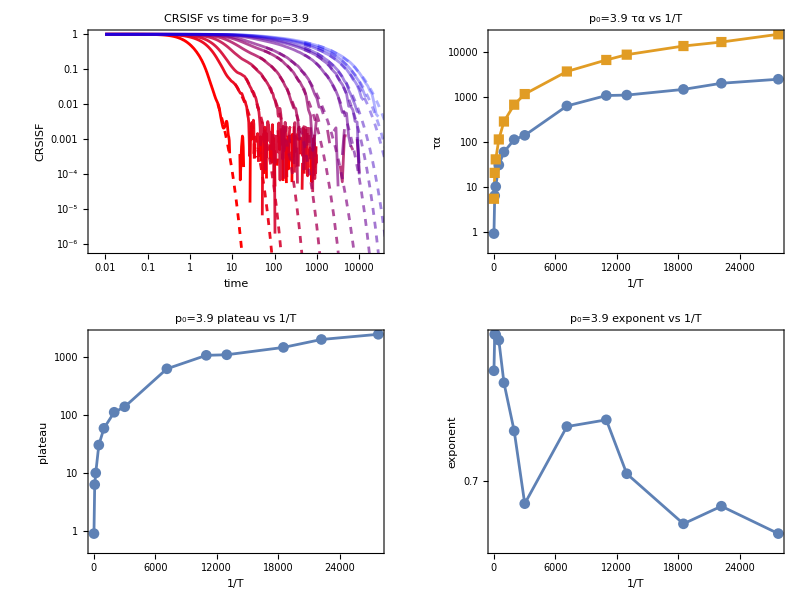

```mathematica
Grid[Partition[{CRSISFFittingPlots[[1]],tauAlphafitingPlot[[1]],plateauPlots[[1]],exponentPlots[[1]]},2]]
```

```mathematica
Table[Export["/home/chengling/Research/updates/05312024/tauAlpha"<>ToString[p0s[[p]]]<>".jpeg",results[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/05312024/tauAlpha3.9.jpeg,/home/chengling/Research/updates/05312024/tauAlpha3.85.jpeg,/home/chengling/Research/updates/05312024/tauAlpha3.825.jpeg,/home/chengling/Research/updates/05312024/tauAlpha3.8.jpeg,/home/chengling/Research/updates/05312024/tauAlpha3.775.jpeg,/home/chengling/Research/updates/05312024/tauAlpha3.75.jpeg}

### fitting log(Tau)

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

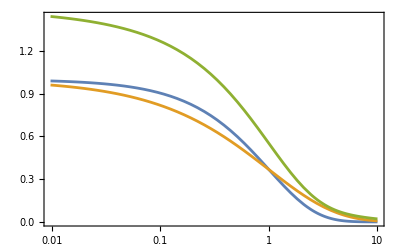

```mathematica
LogLinearPlot[{stretchedExp[t,1,1,1],stretchedExp[t,1,1,0.7],stretchedExp[t,1,1,1]+stretchedExp[t,0.5,1,0.5]},{t,0,10}]
```

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G -(t/τ)^β;
```

```mathematica
fitStartNum={{2,10,20,28.98332354454631,43.181917710603976,52.40218049256373,60.75745364744918,70.43274879137778,74.56208470027373,75.41395136154124,76.2623562138542,76.25356126410557,76.25136268515374},{4.746813237004902,9.4598018063875,11.733682063000668,15.866552523746426,18.857083790143243,23.396892354511074,26.06716697056073,28.407935830446753,33.75497584997275,44.69759769708517,100,100,100,100,100,100,100},{4.181227597599696,6.601632624506163,7.754920469258849,10.846794645005172,16.462632220584393,21.83945522645316,21.252851360922705,23.986133137043076,26.71034271282561,28.95468707418388,29.742850824887917,30.967225782497586,34.954383218327905,42.77645128150349,53.0586027290876,55.991675432346526},{5.5443851977847185,8.543302161661563,10.801556831371771,11.484500787075994,14.159855162331585,16.415770244286062,18.57272413948379,22.353104396049027,23.776138167085982,28.267010584971434,32.38112550556924,42.49938985840521,44.65269580110065,44.10416308353813},{12.275005769964972,13.3900602507303,14.607287299171793,18.46868551379298,21.686557895506116,24.53417261923667,25.778256389405044,32.17535373224476,39.18657032041287,41.68125213915501,45.43737491934978,45,45},{5.22625330341219,8.757313686570457,9.787122180079717,11.705078819553803,14.159218058513453,17.924491941701763,19.168324645208596,25.675629384707115,29.712549254051698,31.78020274296657,34.77161632608988}};
```

```mathematica
fitStartNum={{1,10,20,28.98332354454631,43.181917710603976,52.40218049256373,60.75745364744918,500,500,500,500,500,500},{4.746813237004902,9.4598018063875,11.733682063000668,15.866552523746426,18.857083790143243,23.396892354511074,26.06716697056073,28.407935830446753,100,500,1000,1000,5000,10000,10000,10000,10000},{4.181227597599696,6.601632624506163,5,7,16.462632220584393,21.83945522645316,21.252851360922705,23.986133137043076,26.71034271282561,28.95468707418388,29.742850824887917,30.967225782497586,34.954383218327905,100,500,500},{5.5443851977847185,8.543302161661563,10.801556831371771,11.484500787075994,14.159855162331585,16.415770244286062,18.57272413948379,22.353104396049027,23.776138167085982,100,500,100,100,100},{12.275005769964972,13.3900602507303,14.607287299171793,18.46868551379298,21.686557895506116,24.53417261923667,25.778256389405044,32.17535373224476,39.18657032041287,41.68125213915501,45.43737491934978,45,45},{5.22625330341219,8.757313686570457,9.787122180079717,11.705078819553803,14.159218058513453,17.924491941701763,19.168324645208596,25.675629384707115,29.712549254051698,31.78020274296657,34.77161632608988}};
```

```mathematica
fitStartPos=Table[Table[Position[absTime[[p,i]],_?(#>fitStartNum[[p,i]]&)][[1,1]]+10,{i,Length[fitStartNum[[p]]]}],{p,Length[p0s]}]
```

{{91,191,221,237,73,75,76,94,94,94,94,94,94},{158,188,197,211,218,68,69,70,80,94,391,390,460,491,491,490,490},{153,172,160,175,212,67,67,68,69,70,70,70,71,291,360,360},{165,184,194,197,206,65,66,67,68,80,94,290,290,291},{199,203,207,66,67,68,69,71,72,73,74,74,74},{162,185,190,62,64,66,66,69,70,71,71}}

```mathematica
fitStartPos=Table[Table[If[AllTrue[CRSISFMean[[p,i]],#<0&],Length[CRSISFMean[[p,i]]],Position[CRSISFMean[[p,i]],_?(#<10^-2.5&)][[1,1]]-1],{i,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

```mathematica
fitEndPos=Table[Table[If[AllTrue[CRSISFMean[[p,i]],#>0&],Length[CRSISFMean[[p,i]]],Position[CRSISFMean[[p,i]],_?(#<10^-2.5&)][[1,1]]-1],{i,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{155,218,245,295,81,87,93,104,110,110,112,113,119},{188,228,252,294,298,80,82,90,102,106,474,527,558,560,596,605,624},{166,195,205,247,276,73,77,79,83,87,90,94,99,471,534,557},{174,200,215,225,267,79,81,86,95,101,110,486,513,542},{230,242,273,73,83,89,94,101,102,107,119,122,122},{188,227,250,68,76,84,92,110,109,116,117}}

```mathematica
{{174,232,273,306,82,91,93,106,110,110,112,113,119},{194,230,256,306,310,86,83,96,102,107,493,539,564,564,599,616,625},{185,197,214,248,294,75,78,80,85,92,98,99,102,474,545,567},{182,205,232,245,273,82,83,88,96,103,115,496,525,544},{236,255,290,75,85,96,103,103,113,114,119,123,129},{189,242,255,69,77,86,92,110,111,116,117}}
```

{{174,232,273,306,82,91,93,106,110,110,112,113,119},{194,230,256,306,310,86,83,96,102,107,493,539,564,564,599,616,625},{185,197,214,248,294,75,78,80,85,92,98,99,102,474,545,567},{182,205,232,245,273,82,83,88,96,103,115,496,525,544},{236,255,290,75,85,96,103,103,113,114,119,123,129},{189,242,255,69,77,86,92,110,111,116,117}}

```mathematica
AllTrue[CRSISFMean[[1,1]],#>0&]
```

False

```mathematica
Solve[10^x==0.1,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-1.}}

```mathematica
Normal[CRSISFMean[[1,6,;;]]]
```

{1.,0.999999,0.999995,0.99999,0.999981,0.999971,0.999958,0.999943,0.999926,0.999906,0.999884,0.99986,0.999805,0.999774,0.999705,0.999627,0.99954,0.999445,0.999285,0.999107,0.99884,0.998618,0.99821,0.997757,0.99726,0.99661,0.995786,0.994768,0.99368,0.99224,0.990571,0.988668,0.986355,0.983765,0.980679,0.976813,0.972229,0.966823,0.960288,0.952308,0.943059,0.931814,0.918646,0.902865,0.884882,0.864349,0.841271,0.815772,0.788459,0.759233,0.728204,0.69533,0.661531,0.626911,0.593214,0.559424,0.527269,0.497428,0.469273,0.442224,0.417469,0.395645,0.376741,0.356894,0.339554,0.320263,0.300823,0.279865,0.261139,0.241532,0.221402,0.203593,0.183502,0.162869,0.140786,0.125707,0.110538,0.0936742,0.080051,0.0637999,0.050471,0.0429363,0.0327156,0.0263955,0.0166099,0.00690234,0.00469069,0.00047419,0.00128542,0.00493614,0.00313777,-0.00094492,-0.0000276594,-0.00117291,0.0018284,0.000762127,-0.00186097,0.00131059,-0.0029447,-0.000343101,0.00124985,-0.000829425,-0.00038918,-0.00231518,-0.000547746,0.000658148,0.000485001,-0.000900792,0.00100054,0.000104479}

```mathematica
fitsLogBeta=Table[Table[NonlinearModelFit[Table[{Normal[absTime[[p,T]][[rec]]],Log10[Normal[CRSISFMean[[p,T,rec]]]]},{rec,fitStartPos[[p,T]],fitEndPos[[p,T]]}],{stretchedExp[t,1.0,τ,B],{100000>τ>0.5}},{{B,0.8},{τ,100}},t,MaxIterations->Automatic],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
Table[Table[NonlinearModelFit[Table[{Normal[absTime[[p,T]][[rec]]],Log10[Normal[CRSISFMean[[p,T,rec]]]]},{rec,fitStartPos[[p,T]],fitEndPos[[p,T]]}],{stretchedExp[t,G,τ,β],{1.0>β>0.9,-0.001>G>-1,100000>τ>0.5}},{{β,0.5},{G,Log10[0.5]},{τ,100}},t,MaxIterations->Automatic],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
Table[Table[NonlinearModelFit[Table[{Normal[absTime[[p,T]][[rec]]],Log10[Normal[CRSISFMean[[p,T,rec]]]]},{rec,fitStartPos[[p,T]],fitEndPos[[p,T]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.5,-0.001>G>-1,100000>τ>0.5}},{β,G,τ},t,MaxIterations->Automatic,Method->{"NMinimize",Method->{"RandomSearch","SearchPoints"->500}}],{T,8,10}],{p,1}]
```

```mathematica
{{FittedModel[…],FittedModel[…],FittedModel[…]}}
```

{{FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
fitsLogBeta37
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
Log10[0.99999]
```

-4.34297×10^-6

```mathematica
fitsLog
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
Simplify[Log10[Exp[a *x]]]
```

Log[ⅇ^(a x)]/Log[10]

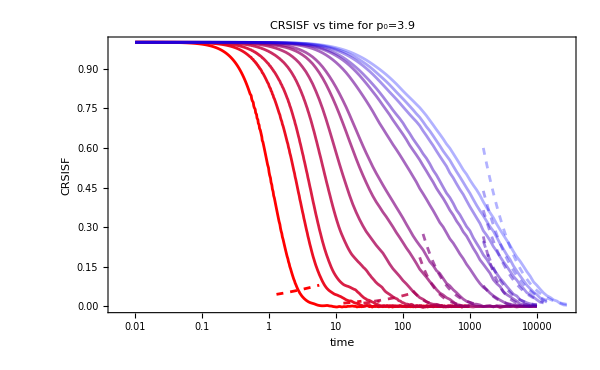
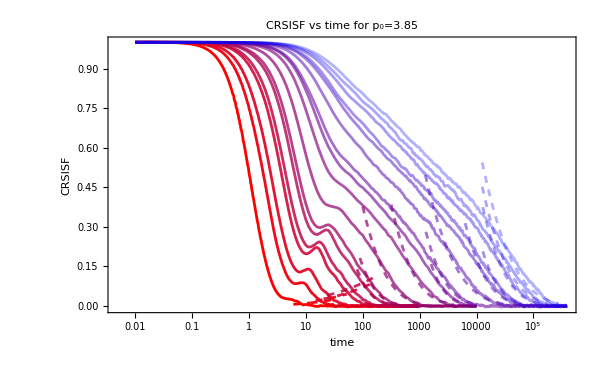
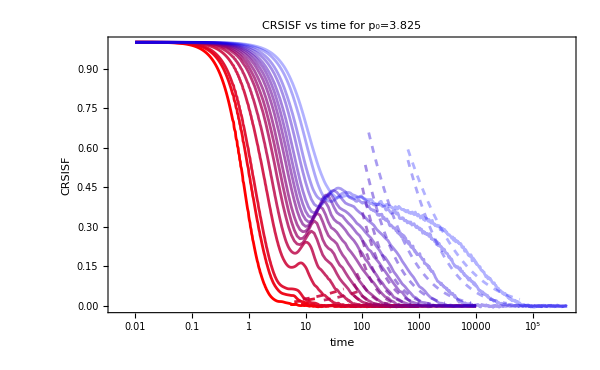
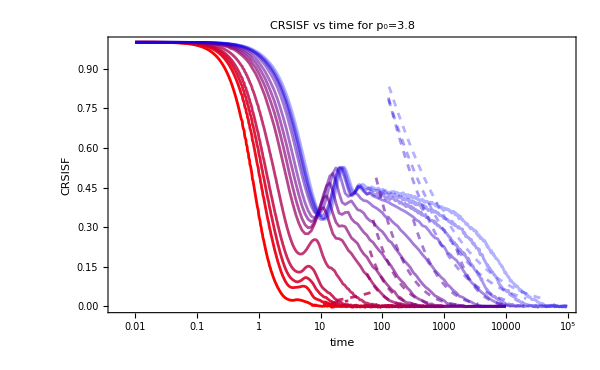
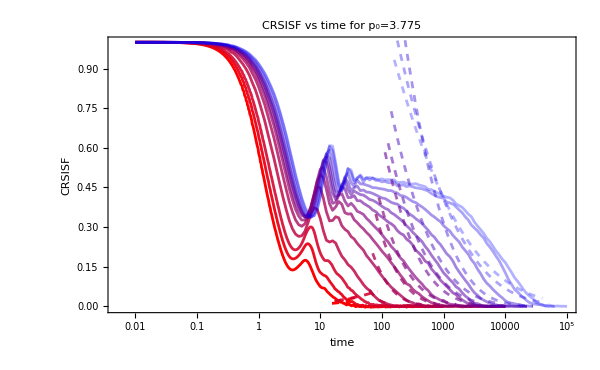
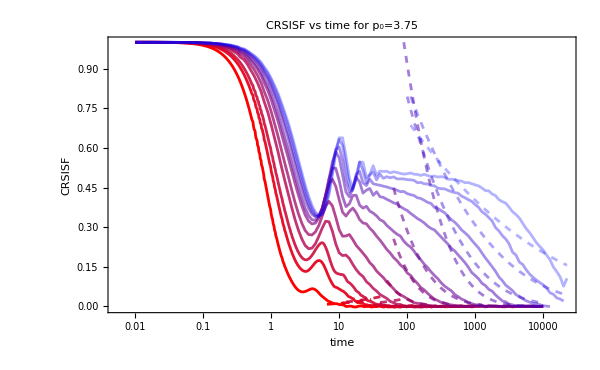

```mathematica
Table[Show[
ListLogLinearPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],Table[LogLinearPlot[10^fitsLogBeta[[p,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotRange->{{0.01,300000},All},PlotStyle->{Dashed,redBluePlotConfig[Length[temperatures[[p]]]][[T]]}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}]
```

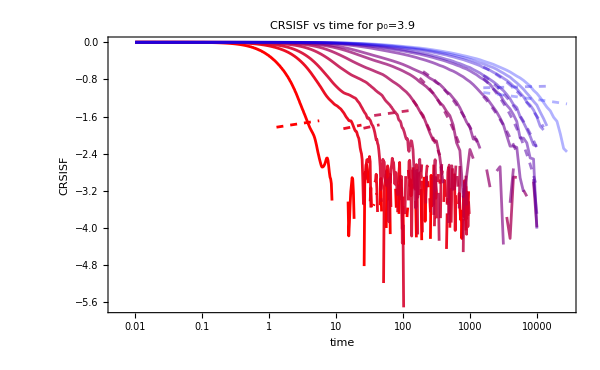
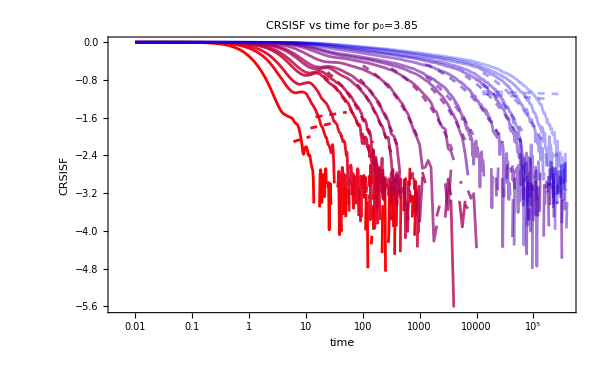
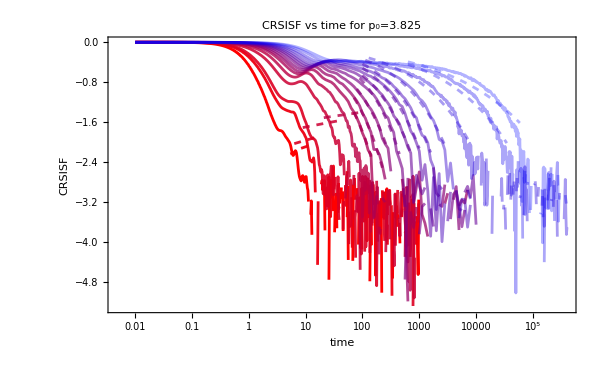
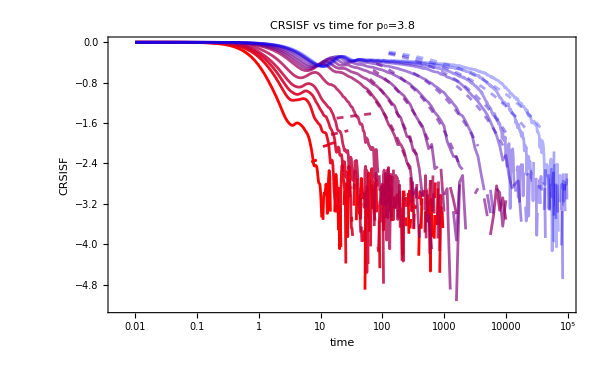
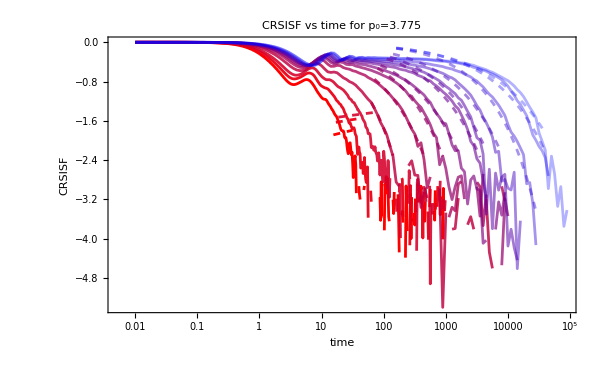
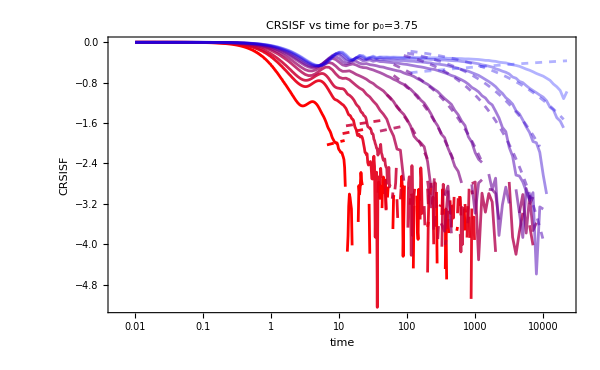

```mathematica
Table[Show[
ListLogLinearPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],Log10[CRSISFMean[[p,T,rec]]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->All],Table[LogLinearPlot[fitsLogBeta[[p,T]][x],{x,absTime[[p,T]][[fitStartPos[[p,T]]]],absTime[[p,T]][[fitEndPos[[p,T]]]]},PlotRange->{{0.01,300000},All},PlotStyle->{Dashed,redBluePlotConfig[Length[temperatures[[p]]]][[T]]}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}]
```